# Equations and material changes for the model

## I-Definitions

```mathematica
ClearAll["Global`*"]
```

### a) Operators

```mathematica
(*Here, by matrix, It means tensor of order 2, and tensor means tensor of order 4*)

tp[a_,b_]:=TensorProduct[a,b]; (*outer product vector*)
PMM[A_,B_]:= Table[Sum[A[[i,j]]*B[[j,k]],{j,1,3}],{i,1,3},{k,1,3}];  (*product matrices*)
tP[A_,B_]:= Table[A[[h,i]]*B[[j,k]],{h,1,3},{j,1,3},{i,1,3},{k,1,3}]; (*Article: outer product tensors*)
tP2[A_,B_]:= Table[A[[h,i]]*B[[j,k]],{h,1,3},{i,1,3},{j,1,3},{k,1,3}];(*Classic: outer product tensors*)

PTT[A_,B_]:=Table[Sum[Sum[A[[h,i]][[j,k]]*B[[j,k]][[l,m]],{j,1,3}],{k,1,3}],{h,1,3},{i,1,3},{l,1,3},{m,1,3}]; (*Product tensors*)

PTM[A_,B_]:=Table[Sum[Sum[A[[h,i]][[j,k]]*B[[j,k]],{j,1,3}],{k,1,3}],{h,1,3},{i,1,3}]; (*Product tensor*Matrix*)

bTranspose[A_]:=Table[A[[j,i]],{i,1,3},{j,1,3}];(*Transpose of matrix*)
bTrace[A_]:=Sum[A[[i,i]],{i,1,3}];(*Trace of a matrix*)
Ps[A_,B_]:=bTrace[PMM[bTranspose[B],A]]; (*Scalar product matrices*)

bI=IdentityMatrix[3]; (*Identity matrix*)
```

```mathematica
Lap[f_]:=D[f,{x,2}]+D[f,{y,2}]+D[f,{z,2}] ;  (*Laplacian*)
bGradT[T_,coor_]:= Table[D[T[[h,i]],{coor[[j]],1}],{h,1,3},{i,1,3},{j,1,3}]; (* Gradient of Matrix*)
bGradTV[Grd_,vec_]:= Table[Sum[Grd[[h,i,j]]*vec[[j]],{j,1,3}],{h,1,3},{i,1,3}];(*Apply the Gradient of a Matrix to a vector*)
```

### b) Quantities

#### Main

```mathematica
(*Velocity field*)
bv={vx[z],0,0};
Dv=Grad[bv,{x,y,z}]; (*Gradient of velocity*) ;
MatrixForm[Dv];
bD=1/2(Dv+Transpose[Dv]); bW=1/2(Dv-Transpose[Dv]);(*Sym and Skw parts of ∇v*)
MatrixForm[bD];
Tr[bD];

(*director*)
bn={Cos[θ[z]],0,Sin[θ[z]]}; 
Dn=Grad[bn,{x,y,z}];
Ln=Lap[bn];
MatrixForm[Ln];
```

```mathematica
bPsi=a0^2 tp[bn,bn]+1/a0(bI-tp[bn,bn]) (*shape tensor Ψ*)
bPsim=1/a0^2 tp[bn,bn]+a0(bI-tp[bn,bn]); (*Ψ^-1*)
bGradTV[bGradT[bPsi,{x,y,z}],bv]
bPsiucd=D[bPsi,t]+bGradTV[bGradT[bPsi,{x,y,z}],bv]-Dv.bPsi-bPsi.Transpose[Dv];(*Ψ^∇codeformational derivative of shape tensor*)
MatrixForm[bPsiucd//FullSimplify];

bTa=-1/2 ρ μ ζ bI; bTa2=-1/2 ρ μ ζ bPsi; (*activity: Subscript[T, a]*)
ΨmB=bI+2/(ρ μ) bTa.bPsi-τ bPsiucd.bPsi;  ΨmB2=bI+2/(ρ μ) bTa2.bPsi-τ bPsiucd.bPsi; (*Ψ^-1 Be=I-2/ρμ Subscript[T, a].Ψ-τΨ^∇.Ψ*)
```

{{a0^2 Cos[θ[z]]^2+(1-Cos[θ[z]]^2)/a0,0,-(Cos[θ[z]] Sin[θ[z]])/a0+a0^2 Cos[θ[z]] Sin[θ[z]]},{0,1/a0,0},{-(Cos[θ[z]] Sin[θ[z]])/a0+a0^2 Cos[θ[z]] Sin[θ[z]],0,a0^2 Sin[θ[z]]^2+(1-Sin[θ[z]]^2)/a0}}

{{{0,0,(2 Cos[θ[z]] Sin[θ[z]] θ'[z])/a0-2 a0^2 Cos[θ[z]] Sin[θ[z]] θ'[z]},{0,0,0},{0,0,-(Cos[θ[z]]^2 θ'[z])/a0+a0^2 Cos[θ[z]]^2 θ'[z]+(Sin[θ[z]]^2 θ'[z])/a0-a0^2 Sin[θ[z]]^2 θ'[z]}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,-(Cos[θ[z]]^2 θ'[z])/a0+a0^2 Cos[θ[z]]^2 θ'[z]+(Sin[θ[z]]^2 θ'[z])/a0-a0^2 Sin[θ[z]]^2 θ'[z]},{0,0,0},{0,0,-(2 Cos[θ[z]] Sin[θ[z]] θ'[z])/a0+2 a0^2 Cos[θ[z]] Sin[θ[z]] θ'[z]}}}

{3,3,3}

0

{{0,0,0},{0,0,0},{0,0,0}}

#### E_i base.

```mathematica
e1={Sin[θ[z]],0,-Cos[θ[z]]};
e2={0,1,0};
E1=1/Sqrt[2](tp[e2,bn]+ tp[bn,e2]);E2=1/Sqrt[2]( tp[e1,bn]+ tp[bn,e1]);
E3=1/Sqrt[2](  tp[e1,e2]+  tp[e2,e1]); E4=1/Sqrt[2](tp[e1,e1]-tp[e2,e2]);
E5=Sqrt[3]/Sqrt[2]( tp[bn,bn]-1/3 bI);E6=1/Sqrt[3] bI;


bTI= PTT[tP[bPsim,bPsim],tP[bPsi,bPsi]];(*identity tensor of order 4*)
```

```mathematica
Subscript[τ, 55]=Subscript[τ, s]+Subscript[τ, d]/(9 a0^3)((4 a0^6+a0^3+4)Cos[2*w]-√2(a0^3-1)^2 Sin[2*w]);
Subscript[τ, 56]=Subscript[τ, d]/(9 a0^3)((2 a0^6+8 a0^3-1)Sin[2*w]+2 √2(-2 a0^6+a0^3+1)Cos[2*w]);
Subscript[τ, 65]=Subscript[τ, d]/(9 a0^3)((-a0^6+8 a0^3+2)Sin[2*w]+2 √2(a0^6+a0^3-2)Cos[2*w]);
Subscript[τ, 66]=Subscript[τ, s]+Subscript[τ, d]/(9 a0^3)(-(4 a0^6+a0^3+4)Cos[2*w]+√2(a0^3-1)^2 Sin[2*w]);

bTtau11 = Subscript[τ, 1] tP2[E1,E1]+ Subscript[τ, 1] tP2[E2,E2]+ Subscript[τ, 2] tP2[E3,E3]+ Subscript[τ, 2] tP2[E4,E4]+Subscript[τ, 55] tP2[E5,E5]+Subscript[τ, 56] tP2[E5,E6]+Subscript[τ, 65] tP2[E6,E5]+Subscript[τ, 66] tP2[E6,E6];
bTtau12 = Subscript[τ, 1] tP2[E1,E1]+ Subscript[τ, 1] tP2[E2,E2]+ Subscript[τ, 2] tP2[E3,E3]+ Subscript[τ, 2] tP2[E4,E4];

bDtau11=PTT[tP[bPsim,bPsim],bTtau11];
bDtau12=PTT[tP[bPsim,bPsim],bTtau12];


ΨmB311=bI+2/(ρ μ) bTa.bPsi-PTM[bDtau11, bPsiucd].bPsi;

(*Ψ^-1 Be*) 
ΨmB312=bI+2/(ρ μ) bTa.bPsi-PTM[bDtau12, bPsiucd].bPsi;
```

#### Check orthonormality of Ei

```mathematica
"E1"
Ps[E1,E1]//Simplify
Ps[E1,E2]
Ps[E1,E3]
Ps[E1,E4]
Ps[E1,E5]
Ps[E1,E6]

"E2"
Ps[E2,E2]//Simplify
Ps[E2,E3]
Ps[E2,E4]//Simplify
Ps[E2,E5]//Simplify
Ps[E2,E6]

"E3"
Ps[E3,E3]//Simplify
Ps[E3,E4]//Simplify
Ps[E3,E5]//Simplify
Ps[E3,E6]//Simplify

"E4"
Ps[E4,E4]//Simplify
Ps[E4,E5]//Simplify
Ps[E4,E6]//Simplify

"E5"
Ps[E5,E5]//Simplify
Ps[E6,E5]//Simplify

"E6"
Ps[E6,E6]//Simplify
```

E1

1

0

0

0

«2 more identical outputs»

E2

1

0

0

0

«1 more identical outputs»

E3

1

0

0

0

E4

1

0

0

E5

1

0

E6

1

#### L_i base.

```mathematica
L1=Sqrt[a0] E1;L2=Sqrt[a0]E2; L3=1/a0 E3; L4=1/a0 E4;
L5=Sqrt[2/3]( a0^2 tp[bn,bn]−1/(2 a0)(bI−tp[bn,bn]));L6=1/Sqrt[3] bPsi;

BL={L1,L2,L3,L4,L5,L6};

bR=tP[bPsim,bPsim];

LtP[A_,B_]:=Table[A[[p,q]]*Sum[Sum[B[[l,k]]*bR[[l,k]][[i,j]],{l,1,3}],{k,1,3}],{p,1,3},{q,1,3},{i,1,3},{j,1,3}];
LPs[A_,B_]:= bTrace[bTranspose[A].(bPsim.B.bPsim)];


bTtau21= Table[0,{i,6},{j,6}];
bTtau22= Table[0,{i,6},{j,6}];

bTtau21[[1,1]]=Subscript[τ, 1];
bTtau21[[2,2]]=Subscript[τ, 1];
bTtau21[[3,3]]=Subscript[τ, 2];
bTtau21[[4,4]]=Subscript[τ, 2];
bTtau21[[5,5]]=Subscript[τ, s]+Subscript[τ, d]*Cos[2*w];
bTtau21[[5,6]]=Subscript[τ, d]*Sin[2*w];
bTtau21[[6,5]]=Subscript[τ, d]*Sin[2*w];
bTtau21[[6,6]]=Subscript[τ, s]-Subscript[τ, d]*Cos[2*w];

bTtau22[[1,1]]=Subscript[τ, 1];
bTtau22[[2,2]]=Subscript[τ, 1];
bTtau22[[3,3]]=Subscript[τ, 2];
bTtau22[[4,4]]=Subscript[τ, 2];

bTt21=Table[0,{i,3},{j,3}];
bTt22=Table[0,{i,3},{j,3}];

For[i=1,i<7,i++,For[j=1,j<7,j++,bTt21=bTt21+bTtau21[[i,j]]*LtP[BL[[i]],BL[[j]]]]];

For[i=1,i<7,i++,For[j=1,j<7,j++,bTt22=bTt22+bTtau22[[i,j]]*LtP[BL[[i]],BL[[j]]]]];
(bTt22-bTtau12)//Simplify//MatrixForm;
(bTt22 )//Simplify//MatrixForm;
(bTtau12)//Simplify//MatrixForm;

bDtau21=PTT[tP[bPsim,bPsim],bTt21];
bDtau22=PTT[tP[bPsim,bPsim],bTt22];

(*Ψ^-1 Be*) 
ΨmB321=bI+2/(ρ μ) bTa.bPsi-PTM[bDtau21, bPsiucd].bPsi;

ΨmB322=bI+2/(ρ μ) bTa.bPsi-PTM[bDtau22, bPsiucd].bPsi;
```

#### Check orthonormality of Li

```mathematica
"E1"
LPs[L1,L1]//Simplify
LPs[L1,L2]//Simplify
LPs[L1,L3]//Simplify
LPs[L1,L4]//Simplify
LPs[L1,L5]//Simplify
LPs[L1,L6]//Simplify

"L2"
LPs[L2,L2]//Simplify
LPs[L2,L3]//Simplify
LPs[L2,L4]//Simplify
LPs[L2,L5]//Simplify
LPs[L2,L6]//Simplify

"L3"
LPs[L3,L3]//Simplify
LPs[L3,L4]//Simplify
LPs[L3,L5]//Simplify
LPs[L3,L6]//Simplify

"L4"
LPs[L4,L4]//Simplify
LPs[L4,L5]//Simplify
LPs[L4,L6]//Simplify

"L5"
LPs[L5,L5]//Simplify
LPs[L6,L5]//Simplify

"L6"
LPs[L6,L6]//Simplify
```

E1

1

0

0

0

«2 more identical outputs»

L2

1

0

0

0

«1 more identical outputs»

L3

1

0

0

0

L4

1

0

0

L5

1

0

L6

1

#### Check Ei and Li differences

```mathematica
BE={E1,E2,E3,E4,E5,E6};
MatrixForm[bTtau11-bTt21]//Simplify
MatrixForm[bTtau12-bTt22]//Simplify
MatrixForm[(bTtau11-bTtau12)/.{Subscript[τ, s]-> 0, Subscript[τ, d]->0}]//Simplify
(*
For[i=1,i<7,i++,
For[j=1,j<7,j++,
Print[{Simplify[Ps[BE[[i]],PTM[bTtau11bis,BE[[j]]]]],i,j}]
]]
*)
(*
For[i=1,i<7,i++,
For[j=1,j<7,j++,
Print[{Simplify[Sum[Sum[Ps[BE[[i]],BL[[p]]]*bTtau21[[p,q]]*LPs[BL[[q]],BE[[j]]],{p,1,6}],{q,1,6}]],i,j}]
]]
*)
```

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

### c) Equations

```mathematica
bT=-p[z]bI+ρ μ (ΨmB-bI)-ρ k Transpose[Dn].Dn;
bh=-ρ μ(1-a0^-3) ΨmB.bn-ρ k Ln;

bT2=-p[z]bI+ρ μ (ΨmB2-bI)-ρ k Transpose[Dn].Dn;
bh2=-ρ μ(1-a0^-3) ΨmB2.bn-ρ k Ln;

bT311=-p[z]bI+ρ μ (ΨmB311-bI)-ρ k Transpose[Dn].Dn;
bh311=-ρ μ(1-a0^-3) ΨmB311.bn-ρ k Ln;
bT312=-p[z]bI+ρ μ (ΨmB312-bI)-ρ k Transpose[Dn].Dn;
bh312=-ρ μ(1-a0^-3) ΨmB312.bn-ρ k Ln;

bT321=-p[z]bI+ρ μ (ΨmB321-bI)-ρ k Transpose[Dn].Dn;
bh321=-ρ μ(1-a0^-3) ΨmB321.bn-ρ k Ln;
bT322=-p[z]bI+ρ μ (ΨmB322-bI)-ρ k Transpose[Dn].Dn;
bh322=-ρ μ(1-a0^-3) ΨmB322.bn-ρ k Ln;
```

#### Equations for linearized problem a) to c)

```mathematica
(* equations for parts a), c) *)
"eq a) and c)"
eq1=Simplify[{D[bT[[1,3]],z],D[bT[[2,3]],z],D[bT[[3,3]],z]}];
MatrixForm[eq1]
eq2=Simplify[Cross[bn,bh]]

(* equations for part b)*)
"eq b)"
eq12=Simplify[{D[bT2[[1,3]],z],D[bT2[[2,3]],z],D[bT2[[3,3]],z]}];
MatrixForm[eq12]
eq22=Simplify[Cross[bn,bh2]]

(* Boundary condition for c)*)
"BC c)"
Dot[bT,{0,0,1}].{1,0,0}//.{z-> L,θ[L]-> 0}
```

eq a) and c)

((μ ρ (4 (-1+a0^3) (-2 a0 ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]]) vx''[z]))/(8 a0^2)
0
-(8 a0^2 p'[z]+2 (-1+a0^3) μ ρ τ (-1-a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx''[z]+4 ρ θ'[z] (-((-1+a0^3) μ τ ((1+a0^3) Cos[2 θ[z]]-(-1+a0^3) Cos[4 θ[z]]) vx'[z])+2 a0 ((-1+a0^3) ζ μ Sin[2 θ[z]]+2 a0 k θ''[z])))/(8 a0^2))

{0,((-1+a0^3) μ ρ τ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z])/(2 a0^2)+k ρ θ''[z],0}

eq b)

((μ ρ (4 (-1+a0^3) (-2 (1+a0^3) ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]]) vx''[z]))/(8 a0^2)
0
-(8 a0^2 p'[z]+2 (-1+a0^3) μ ρ τ (-1-a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx''[z]+4 ρ θ'[z] (2 (-1+a0^6) ζ μ Sin[2 θ[z]]-(-1+a0^3) μ τ ((1+a0^3) Cos[2 θ[z]]-(-1+a0^3) Cos[4 θ[z]]) vx'[z]+4 a0^2 k θ''[z]))/(8 a0^2))

{0,((-1+a0^3) μ ρ τ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z])/(2 a0^2)+k ρ θ''[z],0}

BC c)

(μ ρ τ vx'[L])/a0^2

#### Equations for part d)

```mathematica
"eq d)"

"Base E_i"
"T no zero on its diagnol"
eq1311={D[bT311[[1,3]],z],D[bT311[[2,3]],z],D[bT311[[3,3]],z]};
MatrixForm[eq1311]//FullSimplify
eq2311=Cross[bn,bh311];
eq2311//FullSimplify

"T no zero on its diagnol"
eq1312={D[bT312[[1,3]],z],D[bT312[[2,3]],z],D[bT312[[3,3]],z]};
MatrixForm[eq1312]//FullSimplify
eq2312=Cross[bn,bh312];
eq2312//FullSimplify

"Base L_i"
"T no zero on its diagnol"
eq1321=Simplify[{D[bT321[[1,3]],z],D[bT321[[2,3]],z],D[bT321[[3,3]],z]}];
MatrixForm[eq1321//FullSimplify]
eq2321=Cross[bn,bh321];
eq2321//FullSimplify

"T zero on its diagnol"
eq1322={D[bT322[[1,3]],z],D[bT322[[2,3]],z],D[bT322[[3,3]],z]};
MatrixForm[eq1322//FullSimplify]
eq2322=Cross[bn,bh322];
eq2322//FullSimplify
```

eq d)

Base E_i

T no zero on its diagnol

(-(μ ρ (-8 (-2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+((2 (-1+a0^6) Sin[2 θ[z]]-(1+a0^3)^2 Sin[4 θ[z]]) τ_1+a0^3 Sin[4 θ[z]] (τ_2+3 Cos[2 w] τ_d+3 τ_s)) vx'[z]) θ'[z]-4 ((1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 τ_1+a0^3 Sin[2 θ[z]]^2 (τ_2+3 Cos[2 w] τ_d+3 τ_s)) vx''[z]))/(16 a0^3)
0
(ρ (2 μ Sin[2 θ[z]] ((1-a0^6+(1+a0^3)^2 Cos[2 θ[z]]) τ_1+a0^3 (-2 Cos[θ[z]]^2 τ_2+(Cos[2 w]+2 √2 Sin[2 w]) τ_d+τ_s-3 Cos[2 θ[z]] (Cos[2 w] τ_d+τ_s))) vx''[z]+4 θ'[z] (-2 a0^2 (-1+a0^3) ζ μ Sin[2 θ[z]]+μ ((-((-1+a0^6) Cos[2 θ[z]])+(1+a0^3)^2 Cos[4 θ[z]]) τ_1+a0^3 (-((Cos[2 θ[z]]+Cos[4 θ[z]]) τ_2)-3 Cos[4 θ[z]] (Cos[2 w] τ_d+τ_s)+Cos[2 θ[z]] ((Cos[2 w]+2 √2 Sin[2 w]) τ_d+τ_s))) vx'[z]-4 a0^3 k θ''[z])))/(8 a0^3))

{0,((-1+a0^3) μ ρ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) τ_1 vx'[z])/(2 a0^3)+k ρ θ''[z],0}

T no zero on its diagnol

(-(μ ρ (4 (2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+(-2 (-1+a0^6) Sin[2 θ[z]] τ_1+Sin[4 θ[z]] ((1+a0^3)^2 τ_1-a0^3 τ_2)) vx'[z]) θ'[z]+(-2 (1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 τ_1+a0^3 (-1+Cos[4 θ[z]]) τ_2) vx''[z]))/(8 a0^3)
0
(ρ (2 μ Sin[2 θ[z]] ((1-a0^6+(1+a0^3)^2 Cos[2 θ[z]]) τ_1-2 a0^3 Cos[θ[z]]^2 τ_2) vx''[z]+4 θ'[z] (μ (-((-1+a0^6) Cos[2 θ[z]])+(1+a0^3)^2 Cos[4 θ[z]]) τ_1 vx'[z]-a0^2 (2 (-1+a0^3) ζ μ Sin[2 θ[z]]+a0 μ (Cos[2 θ[z]]+Cos[4 θ[z]]) τ_2 vx'[z]+4 a0 k θ''[z]))))/(8 a0^3))

{0,((-1+a0^3) μ ρ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) τ_1 vx'[z])/(2 a0^3)+k ρ θ''[z],0}

Base L_i

T no zero on its diagnol

(-(μ ρ (-8 (-2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+((2 (-1+a0^6) Sin[2 θ[z]]-(1+a0^3)^2 Sin[4 θ[z]]) τ_1+a0^3 Sin[4 θ[z]] (τ_2+3 Cos[2 w] τ_d+3 τ_s)) vx'[z]) θ'[z]-4 ((1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 τ_1+a0^3 Sin[2 θ[z]]^2 (τ_2+3 Cos[2 w] τ_d+3 τ_s)) vx''[z]))/(16 a0^3)
0
(ρ (2 μ Sin[2 θ[z]] ((1-a0^6+(1+a0^3)^2 Cos[2 θ[z]]) τ_1+a0^3 (-2 Cos[θ[z]]^2 τ_2+(Cos[2 w]+2 √2 Sin[2 w]) τ_d+τ_s-3 Cos[2 θ[z]] (Cos[2 w] τ_d+τ_s))) vx''[z]+4 θ'[z] (-2 a0^2 (-1+a0^3) ζ μ Sin[2 θ[z]]+μ ((-((-1+a0^6) Cos[2 θ[z]])+(1+a0^3)^2 Cos[4 θ[z]]) τ_1+a0^3 (-((Cos[2 θ[z]]+Cos[4 θ[z]]) τ_2)-3 Cos[4 θ[z]] (Cos[2 w] τ_d+τ_s)+Cos[2 θ[z]] ((Cos[2 w]+2 √2 Sin[2 w]) τ_d+τ_s))) vx'[z]-4 a0^3 k θ''[z])))/(8 a0^3))

{0,((-1+a0^3) μ ρ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) τ_1 vx'[z])/(2 a0^3)+k ρ θ''[z],0}

T zero on its diagnol

(-(μ ρ (4 (2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+(-2 (-1+a0^6) Sin[2 θ[z]] τ_1+Sin[4 θ[z]] ((1+a0^3)^2 τ_1-a0^3 τ_2)) vx'[z]) θ'[z]+(-2 (1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 τ_1+a0^3 (-1+Cos[4 θ[z]]) τ_2) vx''[z]))/(8 a0^3)
0
(ρ (2 μ Sin[2 θ[z]] ((1-a0^6+(1+a0^3)^2 Cos[2 θ[z]]) τ_1-2 a0^3 Cos[θ[z]]^2 τ_2) vx''[z]+4 θ'[z] (μ (-((-1+a0^6) Cos[2 θ[z]])+(1+a0^3)^2 Cos[4 θ[z]]) τ_1 vx'[z]-a0^2 (2 (-1+a0^3) ζ μ Sin[2 θ[z]]+a0 μ (Cos[2 θ[z]]+Cos[4 θ[z]]) τ_2 vx'[z]+4 a0 k θ''[z]))))/(8 a0^3))

{0,((-1+a0^3) μ ρ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) τ_1 vx'[z])/(2 a0^3)+k ρ θ''[z],0}

#### Test between the two bases

```mathematica
FullSimplify[eq1311-eq1321]
FullSimplify[eq1312-eq1322]

FullSimplify[eq2311-eq2321]
FullSimplify[eq2312-eq2322]

FullSimplify[(eq1311-eq1312)/.{Subscript[τ, s]->Subscript[τ, 1],Subscript[τ, d]->Subscript[τ, 1]}]


FullSimplify[eq1311-eq1312]
```

{0,0,0}

{0,0,0}

{0,0,0}

«1 more identical outputs»

{3/2 μ ρ Cos[w]^2 Sin[2 θ[z]] τ_1 (4 Cos[2 θ[z]] vx'[z] θ'[z]+Sin[2 θ[z]] vx''[z]),0,1/4 μ ρ Cos[w] τ_1 (4 (-3 Cos[w] Cos[4 θ[z]]+Cos[2 θ[z]] (Cos[w]+2 √2 Sin[w])) vx'[z] θ'[z]+(2 (Cos[w]+2 √2 Sin[w]) Sin[2 θ[z]]-3 Cos[w] Sin[4 θ[z]]) vx''[z])}

{3/4 μ ρ Sin[2 θ[z]] (Cos[2 w] τ_d+τ_s) (4 Cos[2 θ[z]] vx'[z] θ'[z]+Sin[2 θ[z]] vx''[z]),0,1/8 μ ρ (-12 Cos[4 θ[z]] (Cos[2 w] τ_d+τ_s) vx'[z] θ'[z]+4 Cos[2 θ[z]] ((Cos[2 w]+2 √2 Sin[2 w]) τ_d+τ_s) vx'[z] θ'[z]-3 Sin[4 θ[z]] (Cos[2 w] τ_d+τ_s) vx''[z]+2 Sin[2 θ[z]] ((Cos[2 w]+2 √2 Sin[2 w]) τ_d+τ_s) vx''[z])}

### d) Draft and tries

```mathematica
ClearAll["Global`*"]

tp[a_,b_]:=TensorProduct[a,b]; (*outer product*)

tP[A_,B_]:= Table[A[[h,i]]B[[j,k]],{h,1,3},{j,1,3},{i,1,3},{k,1,3}];(*Tensor product or Kronecker Product *)

(*Multiplication between two Fourth-order tensors*)
PTT[A_,B_]:=Table[Sum[Sum[A[[h,i]][[j,k]]B[[j,k]][[l,m]],{j,1,3}],{k,1,3}],{h,1,3},{i,1,3},{l,1,3},{m,1,3}];

(*Multiplication between Fourth-order tensors and Second order Tensor*)
PTM[A_,B_]:=Table[Sum[Sum[A[[h,i]][[j,k]]B[[j,k]],{j,1,3}],{k,1,3}],{h,1,3},{i,1,3}];

PMM[A_,B_]:= Table[Sum[A[[i,j]]*B[[j,k]],{j,1,3}],{i,1,3},{k,1,3}]; 
bTranspose[A_]:=Table[A[[j,i]],{i,1,3},{j,1,3}];
bTrace[A_]:=Sum[A[[i,i]],{i,1,3}];
Ps[A_,B_]:=bTrace[PMM[bTranspose[B],A]];
```

```mathematica
(*vectors*)
ba=Array[Subscript[a,##]&,3];
bb=Array[Subscript[b,##]&,3];
bC = tp[ba,bb]; (*Tensor of order two*)

(*Tensors of order 2*)
bA=Array[Subscript[a,##]&,{3,3}];
bB=Array[Subscript[b,##]&,{3,3}];
bbD = tP[bA,bB]; (*Tensor of order 4*)

(*Tensors of order 2*)
bbA=Array[Subscript[a,##]&,{3,3,3,3}];
bbB=Array[Subscript[b,##]&,{3,3,3,3}];
bbC = PTT[bbA,bbB]; (*Tensor of order 4*)
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
"Check outer product between vectors a and b"
MatrixForm[bC]
TensorRank[bC]

"Check outer product between tensors A and B"
MatrixForm[bbD]
TensorRank[bbD]
bbD[[3,2]][[1,3]]
bbD[[3,2,1,3]]
"Check Tensor product between tensors 𝔸 and 𝔹"
MatrixForm[bbC]
TensorRank[bbC]
bbC[[1,3]][[3,2]]
```

Check outer product between vectors a and b

(a_1 b_1 | a_1 b_2 | a_1 b_3
a_2 b_1 | a_2 b_2 | a_2 b_3
a_3 b_1 | a_3 b_2 | a_3 b_3)

2

Check outer product between tensors A and B

((a_(1,1) b_(1,1) | a_(1,1) b_(1,2) | a_(1,1) b_(1,3)
a_(1,2) b_(1,1) | a_(1,2) b_(1,2) | a_(1,2) b_(1,3)
a_(1,3) b_(1,1) | a_(1,3) b_(1,2) | a_(1,3) b_(1,3)) | (a_(1,1) b_(2,1) | a_(1,1) b_(2,2) | a_(1,1) b_(2,3)
a_(1,2) b_(2,1) | a_(1,2) b_(2,2) | a_(1,2) b_(2,3)
a_(1,3) b_(2,1) | a_(1,3) b_(2,2) | a_(1,3) b_(2,3)) | (a_(1,1) b_(3,1) | a_(1,1) b_(3,2) | a_(1,1) b_(3,3)
a_(1,2) b_(3,1) | a_(1,2) b_(3,2) | a_(1,2) b_(3,3)
a_(1,3) b_(3,1) | a_(1,3) b_(3,2) | a_(1,3) b_(3,3))
(a_(2,1) b_(1,1) | a_(2,1) b_(1,2) | a_(2,1) b_(1,3)
a_(2,2) b_(1,1) | a_(2,2) b_(1,2) | a_(2,2) b_(1,3)
a_(2,3) b_(1,1) | a_(2,3) b_(1,2) | a_(2,3) b_(1,3)) | (a_(2,1) b_(2,1) | a_(2,1) b_(2,2) | a_(2,1) b_(2,3)
a_(2,2) b_(2,1) | a_(2,2) b_(2,2) | a_(2,2) b_(2,3)
a_(2,3) b_(2,1) | a_(2,3) b_(2,2) | a_(2,3) b_(2,3)) | (a_(2,1) b_(3,1) | a_(2,1) b_(3,2) | a_(2,1) b_(3,3)
a_(2,2) b_(3,1) | a_(2,2) b_(3,2) | a_(2,2) b_(3,3)
a_(2,3) b_(3,1) | a_(2,3) b_(3,2) | a_(2,3) b_(3,3))
(a_(3,1) b_(1,1) | a_(3,1) b_(1,2) | a_(3,1) b_(1,3)
a_(3,2) b_(1,1) | a_(3,2) b_(1,2) | a_(3,2) b_(1,3)
a_(3,3) b_(1,1) | a_(3,3) b_(1,2) | a_(3,3) b_(1,3)) | (a_(3,1) b_(2,1) | a_(3,1) b_(2,2) | a_(3,1) b_(2,3)
a_(3,2) b_(2,1) | a_(3,2) b_(2,2) | a_(3,2) b_(2,3)
a_(3,3) b_(2,1) | a_(3,3) b_(2,2) | a_(3,3) b_(2,3)) | (a_(3,1) b_(3,1) | a_(3,1) b_(3,2) | a_(3,1) b_(3,3)
a_(3,2) b_(3,1) | a_(3,2) b_(3,2) | a_(3,2) b_(3,3)
a_(3,3) b_(3,1) | a_(3,3) b_(3,2) | a_(3,3) b_(3,3)))

4

a_(3,1) b_(2,3)

a_(3,1) b_(2,3)

Check Tensor product between tensors 𝔸 and 𝔹

((a_(1,1,1,1) b_(1,1,1,1)+a_(1,1,1,2) b_(1,2,1,1)+a_(1,1,1,3) b_(1,3,1,1)+a_(1,1,2,1) b_(2,1,1,1)+a_(1,1,2,2) b_(2,2,1,1)+a_(1,1,2,3) b_(2,3,1,1)+a_(1,1,3,1) b_(3,1,1,1)+a_(1,1,3,2) b_(3,2,1,1)+a_(1,1,3,3) b_(3,3,1,1) | a_(1,1,1,1) b_(1,1,1,2)+a_(1,1,1,2) b_(1,2,1,2)+a_(1,1,1,3) b_(1,3,1,2)+a_(1,1,2,1) b_(2,1,1,2)+a_(1,1,2,2) b_(2,2,1,2)+a_(1,1,2,3) b_(2,3,1,2)+a_(1,1,3,1) b_(3,1,1,2)+a_(1,1,3,2) b_(3,2,1,2)+a_(1,1,3,3) b_(3,3,1,2) | a_(1,1,1,1) b_(1,1,1,3)+a_(1,1,1,2) b_(1,2,1,3)+a_(1,1,1,3) b_(1,3,1,3)+a_(1,1,2,1) b_(2,1,1,3)+a_(1,1,2,2) b_(2,2,1,3)+a_(1,1,2,3) b_(2,3,1,3)+a_(1,1,3,1) b_(3,1,1,3)+a_(1,1,3,2) b_(3,2,1,3)+a_(1,1,3,3) b_(3,3,1,3)
a_(1,1,1,1) b_(1,1,2,1)+a_(1,1,1,2) b_(1,2,2,1)+a_(1,1,1,3) b_(1,3,2,1)+a_(1,1,2,1) b_(2,1,2,1)+a_(1,1,2,2) b_(2,2,2,1)+a_(1,1,2,3) b_(2,3,2,1)+a_(1,1,3,1) b_(3,1,2,1)+a_(1,1,3,2) b_(3,2,2,1)+a_(1,1,3,3) b_(3,3,2,1) | a_(1,1,1,1) b_(1,1,2,2)+a_(1,1,1,2) b_(1,2,2,2)+a_(1,1,1,3) b_(1,3,2,2)+a_(1,1,2,1) b_(2,1,2,2)+a_(1,1,2,2) b_(2,2,2,2)+a_(1,1,2,3) b_(2,3,2,2)+a_(1,1,3,1) b_(3,1,2,2)+a_(1,1,3,2) b_(3,2,2,2)+a_(1,1,3,3) b_(3,3,2,2) | a_(1,1,1,1) b_(1,1,2,3)+a_(1,1,1,2) b_(1,2,2,3)+a_(1,1,1,3) b_(1,3,2,3)+a_(1,1,2,1) b_(2,1,2,3)+a_(1,1,2,2) b_(2,2,2,3)+a_(1,1,2,3) b_(2,3,2,3)+a_(1,1,3,1) b_(3,1,2,3)+a_(1,1,3,2) b_(3,2,2,3)+a_(1,1,3,3) b_(3,3,2,3)
a_(1,1,1,1) b_(1,1,3,1)+a_(1,1,1,2) b_(1,2,3,1)+a_(1,1,1,3) b_(1,3,3,1)+a_(1,1,2,1) b_(2,1,3,1)+a_(1,1,2,2) b_(2,2,3,1)+a_(1,1,2,3) b_(2,3,3,1)+a_(1,1,3,1) b_(3,1,3,1)+a_(1,1,3,2) b_(3,2,3,1)+a_(1,1,3,3) b_(3,3,3,1) | a_(1,1,1,1) b_(1,1,3,2)+a_(1,1,1,2) b_(1,2,3,2)+a_(1,1,1,3) b_(1,3,3,2)+a_(1,1,2,1) b_(2,1,3,2)+a_(1,1,2,2) b_(2,2,3,2)+a_(1,1,2,3) b_(2,3,3,2)+a_(1,1,3,1) b_(3,1,3,2)+a_(1,1,3,2) b_(3,2,3,2)+a_(1,1,3,3) b_(3,3,3,2) | a_(1,1,1,1) b_(1,1,3,3)+a_(1,1,1,2) b_(1,2,3,3)+a_(1,1,1,3) b_(1,3,3,3)+a_(1,1,2,1) b_(2,1,3,3)+a_(1,1,2,2) b_(2,2,3,3)+a_(1,1,2,3) b_(2,3,3,3)+a_(1,1,3,1) b_(3,1,3,3)+a_(1,1,3,2) b_(3,2,3,3)+a_(1,1,3,3) b_(3,3,3,3)) | (a_(1,2,1,1) b_(1,1,1,1)+a_(1,2,1,2) b_(1,2,1,1)+a_(1,2,1,3) b_(1,3,1,1)+a_(1,2,2,1) b_(2,1,1,1)+a_(1,2,2,2) b_(2,2,1,1)+a_(1,2,2,3) b_(2,3,1,1)+a_(1,2,3,1) b_(3,1,1,1)+a_(1,2,3,2) b_(3,2,1,1)+a_(1,2,3,3) b_(3,3,1,1) | a_(1,2,1,1) b_(1,1,1,2)+a_(1,2,1,2) b_(1,2,1,2)+a_(1,2,1,3) b_(1,3,1,2)+a_(1,2,2,1) b_(2,1,1,2)+a_(1,2,2,2) b_(2,2,1,2)+a_(1,2,2,3) b_(2,3,1,2)+a_(1,2,3,1) b_(3,1,1,2)+a_(1,2,3,2) b_(3,2,1,2)+a_(1,2,3,3) b_(3,3,1,2) | a_(1,2,1,1) b_(1,1,1,3)+a_(1,2,1,2) b_(1,2,1,3)+a_(1,2,1,3) b_(1,3,1,3)+a_(1,2,2,1) b_(2,1,1,3)+a_(1,2,2,2) b_(2,2,1,3)+a_(1,2,2,3) b_(2,3,1,3)+a_(1,2,3,1) b_(3,1,1,3)+a_(1,2,3,2) b_(3,2,1,3)+a_(1,2,3,3) b_(3,3,1,3)
a_(1,2,1,1) b_(1,1,2,1)+a_(1,2,1,2) b_(1,2,2,1)+a_(1,2,1,3) b_(1,3,2,1)+a_(1,2,2,1) b_(2,1,2,1)+a_(1,2,2,2) b_(2,2,2,1)+a_(1,2,2,3) b_(2,3,2,1)+a_(1,2,3,1) b_(3,1,2,1)+a_(1,2,3,2) b_(3,2,2,1)+a_(1,2,3,3) b_(3,3,2,1) | a_(1,2,1,1) b_(1,1,2,2)+a_(1,2,1,2) b_(1,2,2,2)+a_(1,2,1,3) b_(1,3,2,2)+a_(1,2,2,1) b_(2,1,2,2)+a_(1,2,2,2) b_(2,2,2,2)+a_(1,2,2,3) b_(2,3,2,2)+a_(1,2,3,1) b_(3,1,2,2)+a_(1,2,3,2) b_(3,2,2,2)+a_(1,2,3,3) b_(3,3,2,2) | a_(1,2,1,1) b_(1,1,2,3)+a_(1,2,1,2) b_(1,2,2,3)+a_(1,2,1,3) b_(1,3,2,3)+a_(1,2,2,1) b_(2,1,2,3)+a_(1,2,2,2) b_(2,2,2,3)+a_(1,2,2,3) b_(2,3,2,3)+a_(1,2,3,1) b_(3,1,2,3)+a_(1,2,3,2) b_(3,2,2,3)+a_(1,2,3,3) b_(3,3,2,3)
a_(1,2,1,1) b_(1,1,3,1)+a_(1,2,1,2) b_(1,2,3,1)+a_(1,2,1,3) b_(1,3,3,1)+a_(1,2,2,1) b_(2,1,3,1)+a_(1,2,2,2) b_(2,2,3,1)+a_(1,2,2,3) b_(2,3,3,1)+a_(1,2,3,1) b_(3,1,3,1)+a_(1,2,3,2) b_(3,2,3,1)+a_(1,2,3,3) b_(3,3,3,1) | a_(1,2,1,1) b_(1,1,3,2)+a_(1,2,1,2) b_(1,2,3,2)+a_(1,2,1,3) b_(1,3,3,2)+a_(1,2,2,1) b_(2,1,3,2)+a_(1,2,2,2) b_(2,2,3,2)+a_(1,2,2,3) b_(2,3,3,2)+a_(1,2,3,1) b_(3,1,3,2)+a_(1,2,3,2) b_(3,2,3,2)+a_(1,2,3,3) b_(3,3,3,2) | a_(1,2,1,1) b_(1,1,3,3)+a_(1,2,1,2) b_(1,2,3,3)+a_(1,2,1,3) b_(1,3,3,3)+a_(1,2,2,1) b_(2,1,3,3)+a_(1,2,2,2) b_(2,2,3,3)+a_(1,2,2,3) b_(2,3,3,3)+a_(1,2,3,1) b_(3,1,3,3)+a_(1,2,3,2) b_(3,2,3,3)+a_(1,2,3,3) b_(3,3,3,3)) | (a_(1,3,1,1) b_(1,1,1,1)+a_(1,3,1,2) b_(1,2,1,1)+a_(1,3,1,3) b_(1,3,1,1)+a_(1,3,2,1) b_(2,1,1,1)+a_(1,3,2,2) b_(2,2,1,1)+a_(1,3,2,3) b_(2,3,1,1)+a_(1,3,3,1) b_(3,1,1,1)+a_(1,3,3,2) b_(3,2,1,1)+a_(1,3,3,3) b_(3,3,1,1) | a_(1,3,1,1) b_(1,1,1,2)+a_(1,3,1,2) b_(1,2,1,2)+a_(1,3,1,3) b_(1,3,1,2)+a_(1,3,2,1) b_(2,1,1,2)+a_(1,3,2,2) b_(2,2,1,2)+a_(1,3,2,3) b_(2,3,1,2)+a_(1,3,3,1) b_(3,1,1,2)+a_(1,3,3,2) b_(3,2,1,2)+a_(1,3,3,3) b_(3,3,1,2) | a_(1,3,1,1) b_(1,1,1,3)+a_(1,3,1,2) b_(1,2,1,3)+a_(1,3,1,3) b_(1,3,1,3)+a_(1,3,2,1) b_(2,1,1,3)+a_(1,3,2,2) b_(2,2,1,3)+a_(1,3,2,3) b_(2,3,1,3)+a_(1,3,3,1) b_(3,1,1,3)+a_(1,3,3,2) b_(3,2,1,3)+a_(1,3,3,3) b_(3,3,1,3)
a_(1,3,1,1) b_(1,1,2,1)+a_(1,3,1,2) b_(1,2,2,1)+a_(1,3,1,3) b_(1,3,2,1)+a_(1,3,2,1) b_(2,1,2,1)+a_(1,3,2,2) b_(2,2,2,1)+a_(1,3,2,3) b_(2,3,2,1)+a_(1,3,3,1) b_(3,1,2,1)+a_(1,3,3,2) b_(3,2,2,1)+a_(1,3,3,3) b_(3,3,2,1) | a_(1,3,1,1) b_(1,1,2,2)+a_(1,3,1,2) b_(1,2,2,2)+a_(1,3,1,3) b_(1,3,2,2)+a_(1,3,2,1) b_(2,1,2,2)+a_(1,3,2,2) b_(2,2,2,2)+a_(1,3,2,3) b_(2,3,2,2)+a_(1,3,3,1) b_(3,1,2,2)+a_(1,3,3,2) b_(3,2,2,2)+a_(1,3,3,3) b_(3,3,2,2) | a_(1,3,1,1) b_(1,1,2,3)+a_(1,3,1,2) b_(1,2,2,3)+a_(1,3,1,3) b_(1,3,2,3)+a_(1,3,2,1) b_(2,1,2,3)+a_(1,3,2,2) b_(2,2,2,3)+a_(1,3,2,3) b_(2,3,2,3)+a_(1,3,3,1) b_(3,1,2,3)+a_(1,3,3,2) b_(3,2,2,3)+a_(1,3,3,3) b_(3,3,2,3)
a_(1,3,1,1) b_(1,1,3,1)+a_(1,3,1,2) b_(1,2,3,1)+a_(1,3,1,3) b_(1,3,3,1)+a_(1,3,2,1) b_(2,1,3,1)+a_(1,3,2,2) b_(2,2,3,1)+a_(1,3,2,3) b_(2,3,3,1)+a_(1,3,3,1) b_(3,1,3,1)+a_(1,3,3,2) b_(3,2,3,1)+a_(1,3,3,3) b_(3,3,3,1) | a_(1,3,1,1) b_(1,1,3,2)+a_(1,3,1,2) b_(1,2,3,2)+a_(1,3,1,3) b_(1,3,3,2)+a_(1,3,2,1) b_(2,1,3,2)+a_(1,3,2,2) b_(2,2,3,2)+a_(1,3,2,3) b_(2,3,3,2)+a_(1,3,3,1) b_(3,1,3,2)+a_(1,3,3,2) b_(3,2,3,2)+a_(1,3,3,3) b_(3,3,3,2) | a_(1,3,1,1) b_(1,1,3,3)+a_(1,3,1,2) b_(1,2,3,3)+a_(1,3,1,3) b_(1,3,3,3)+a_(1,3,2,1) b_(2,1,3,3)+a_(1,3,2,2) b_(2,2,3,3)+a_(1,3,2,3) b_(2,3,3,3)+a_(1,3,3,1) b_(3,1,3,3)+a_(1,3,3,2) b_(3,2,3,3)+a_(1,3,3,3) b_(3,3,3,3))
(a_(2,1,1,1) b_(1,1,1,1)+a_(2,1,1,2) b_(1,2,1,1)+a_(2,1,1,3) b_(1,3,1,1)+a_(2,1,2,1) b_(2,1,1,1)+a_(2,1,2,2) b_(2,2,1,1)+a_(2,1,2,3) b_(2,3,1,1)+a_(2,1,3,1) b_(3,1,1,1)+a_(2,1,3,2) b_(3,2,1,1)+a_(2,1,3,3) b_(3,3,1,1) | a_(2,1,1,1) b_(1,1,1,2)+a_(2,1,1,2) b_(1,2,1,2)+a_(2,1,1,3) b_(1,3,1,2)+a_(2,1,2,1) b_(2,1,1,2)+a_(2,1,2,2) b_(2,2,1,2)+a_(2,1,2,3) b_(2,3,1,2)+a_(2,1,3,1) b_(3,1,1,2)+a_(2,1,3,2) b_(3,2,1,2)+a_(2,1,3,3) b_(3,3,1,2) | a_(2,1,1,1) b_(1,1,1,3)+a_(2,1,1,2) b_(1,2,1,3)+a_(2,1,1,3) b_(1,3,1,3)+a_(2,1,2,1) b_(2,1,1,3)+a_(2,1,2,2) b_(2,2,1,3)+a_(2,1,2,3) b_(2,3,1,3)+a_(2,1,3,1) b_(3,1,1,3)+a_(2,1,3,2) b_(3,2,1,3)+a_(2,1,3,3) b_(3,3,1,3)
a_(2,1,1,1) b_(1,1,2,1)+a_(2,1,1,2) b_(1,2,2,1)+a_(2,1,1,3) b_(1,3,2,1)+a_(2,1,2,1) b_(2,1,2,1)+a_(2,1,2,2) b_(2,2,2,1)+a_(2,1,2,3) b_(2,3,2,1)+a_(2,1,3,1) b_(3,1,2,1)+a_(2,1,3,2) b_(3,2,2,1)+a_(2,1,3,3) b_(3,3,2,1) | a_(2,1,1,1) b_(1,1,2,2)+a_(2,1,1,2) b_(1,2,2,2)+a_(2,1,1,3) b_(1,3,2,2)+a_(2,1,2,1) b_(2,1,2,2)+a_(2,1,2,2) b_(2,2,2,2)+a_(2,1,2,3) b_(2,3,2,2)+a_(2,1,3,1) b_(3,1,2,2)+a_(2,1,3,2) b_(3,2,2,2)+a_(2,1,3,3) b_(3,3,2,2) | a_(2,1,1,1) b_(1,1,2,3)+a_(2,1,1,2) b_(1,2,2,3)+a_(2,1,1,3) b_(1,3,2,3)+a_(2,1,2,1) b_(2,1,2,3)+a_(2,1,2,2) b_(2,2,2,3)+a_(2,1,2,3) b_(2,3,2,3)+a_(2,1,3,1) b_(3,1,2,3)+a_(2,1,3,2) b_(3,2,2,3)+a_(2,1,3,3) b_(3,3,2,3)
a_(2,1,1,1) b_(1,1,3,1)+a_(2,1,1,2) b_(1,2,3,1)+a_(2,1,1,3) b_(1,3,3,1)+a_(2,1,2,1) b_(2,1,3,1)+a_(2,1,2,2) b_(2,2,3,1)+a_(2,1,2,3) b_(2,3,3,1)+a_(2,1,3,1) b_(3,1,3,1)+a_(2,1,3,2) b_(3,2,3,1)+a_(2,1,3,3) b_(3,3,3,1) | a_(2,1,1,1) b_(1,1,3,2)+a_(2,1,1,2) b_(1,2,3,2)+a_(2,1,1,3) b_(1,3,3,2)+a_(2,1,2,1) b_(2,1,3,2)+a_(2,1,2,2) b_(2,2,3,2)+a_(2,1,2,3) b_(2,3,3,2)+a_(2,1,3,1) b_(3,1,3,2)+a_(2,1,3,2) b_(3,2,3,2)+a_(2,1,3,3) b_(3,3,3,2) | a_(2,1,1,1) b_(1,1,3,3)+a_(2,1,1,2) b_(1,2,3,3)+a_(2,1,1,3) b_(1,3,3,3)+a_(2,1,2,1) b_(2,1,3,3)+a_(2,1,2,2) b_(2,2,3,3)+a_(2,1,2,3) b_(2,3,3,3)+a_(2,1,3,1) b_(3,1,3,3)+a_(2,1,3,2) b_(3,2,3,3)+a_(2,1,3,3) b_(3,3,3,3)) | (a_(2,2,1,1) b_(1,1,1,1)+a_(2,2,1,2) b_(1,2,1,1)+a_(2,2,1,3) b_(1,3,1,1)+a_(2,2,2,1) b_(2,1,1,1)+a_(2,2,2,2) b_(2,2,1,1)+a_(2,2,2,3) b_(2,3,1,1)+a_(2,2,3,1) b_(3,1,1,1)+a_(2,2,3,2) b_(3,2,1,1)+a_(2,2,3,3) b_(3,3,1,1) | a_(2,2,1,1) b_(1,1,1,2)+a_(2,2,1,2) b_(1,2,1,2)+a_(2,2,1,3) b_(1,3,1,2)+a_(2,2,2,1) b_(2,1,1,2)+a_(2,2,2,2) b_(2,2,1,2)+a_(2,2,2,3) b_(2,3,1,2)+a_(2,2,3,1) b_(3,1,1,2)+a_(2,2,3,2) b_(3,2,1,2)+a_(2,2,3,3) b_(3,3,1,2) | a_(2,2,1,1) b_(1,1,1,3)+a_(2,2,1,2) b_(1,2,1,3)+a_(2,2,1,3) b_(1,3,1,3)+a_(2,2,2,1) b_(2,1,1,3)+a_(2,2,2,2) b_(2,2,1,3)+a_(2,2,2,3) b_(2,3,1,3)+a_(2,2,3,1) b_(3,1,1,3)+a_(2,2,3,2) b_(3,2,1,3)+a_(2,2,3,3) b_(3,3,1,3)
a_(2,2,1,1) b_(1,1,2,1)+a_(2,2,1,2) b_(1,2,2,1)+a_(2,2,1,3) b_(1,3,2,1)+a_(2,2,2,1) b_(2,1,2,1)+a_(2,2,2,2) b_(2,2,2,1)+a_(2,2,2,3) b_(2,3,2,1)+a_(2,2,3,1) b_(3,1,2,1)+a_(2,2,3,2) b_(3,2,2,1)+a_(2,2,3,3) b_(3,3,2,1) | a_(2,2,1,1) b_(1,1,2,2)+a_(2,2,1,2) b_(1,2,2,2)+a_(2,2,1,3) b_(1,3,2,2)+a_(2,2,2,1) b_(2,1,2,2)+a_(2,2,2,2) b_(2,2,2,2)+a_(2,2,2,3) b_(2,3,2,2)+a_(2,2,3,1) b_(3,1,2,2)+a_(2,2,3,2) b_(3,2,2,2)+a_(2,2,3,3) b_(3,3,2,2) | a_(2,2,1,1) b_(1,1,2,3)+a_(2,2,1,2) b_(1,2,2,3)+a_(2,2,1,3) b_(1,3,2,3)+a_(2,2,2,1) b_(2,1,2,3)+a_(2,2,2,2) b_(2,2,2,3)+a_(2,2,2,3) b_(2,3,2,3)+a_(2,2,3,1) b_(3,1,2,3)+a_(2,2,3,2) b_(3,2,2,3)+a_(2,2,3,3) b_(3,3,2,3)
a_(2,2,1,1) b_(1,1,3,1)+a_(2,2,1,2) b_(1,2,3,1)+a_(2,2,1,3) b_(1,3,3,1)+a_(2,2,2,1) b_(2,1,3,1)+a_(2,2,2,2) b_(2,2,3,1)+a_(2,2,2,3) b_(2,3,3,1)+a_(2,2,3,1) b_(3,1,3,1)+a_(2,2,3,2) b_(3,2,3,1)+a_(2,2,3,3) b_(3,3,3,1) | a_(2,2,1,1) b_(1,1,3,2)+a_(2,2,1,2) b_(1,2,3,2)+a_(2,2,1,3) b_(1,3,3,2)+a_(2,2,2,1) b_(2,1,3,2)+a_(2,2,2,2) b_(2,2,3,2)+a_(2,2,2,3) b_(2,3,3,2)+a_(2,2,3,1) b_(3,1,3,2)+a_(2,2,3,2) b_(3,2,3,2)+a_(2,2,3,3) b_(3,3,3,2) | a_(2,2,1,1) b_(1,1,3,3)+a_(2,2,1,2) b_(1,2,3,3)+a_(2,2,1,3) b_(1,3,3,3)+a_(2,2,2,1) b_(2,1,3,3)+a_(2,2,2,2) b_(2,2,3,3)+a_(2,2,2,3) b_(2,3,3,3)+a_(2,2,3,1) b_(3,1,3,3)+a_(2,2,3,2) b_(3,2,3,3)+a_(2,2,3,3) b_(3,3,3,3)) | (a_(2,3,1,1) b_(1,1,1,1)+a_(2,3,1,2) b_(1,2,1,1)+a_(2,3,1,3) b_(1,3,1,1)+a_(2,3,2,1) b_(2,1,1,1)+a_(2,3,2,2) b_(2,2,1,1)+a_(2,3,2,3) b_(2,3,1,1)+a_(2,3,3,1) b_(3,1,1,1)+a_(2,3,3,2) b_(3,2,1,1)+a_(2,3,3,3) b_(3,3,1,1) | a_(2,3,1,1) b_(1,1,1,2)+a_(2,3,1,2) b_(1,2,1,2)+a_(2,3,1,3) b_(1,3,1,2)+a_(2,3,2,1) b_(2,1,1,2)+a_(2,3,2,2) b_(2,2,1,2)+a_(2,3,2,3) b_(2,3,1,2)+a_(2,3,3,1) b_(3,1,1,2)+a_(2,3,3,2) b_(3,2,1,2)+a_(2,3,3,3) b_(3,3,1,2) | a_(2,3,1,1) b_(1,1,1,3)+a_(2,3,1,2) b_(1,2,1,3)+a_(2,3,1,3) b_(1,3,1,3)+a_(2,3,2,1) b_(2,1,1,3)+a_(2,3,2,2) b_(2,2,1,3)+a_(2,3,2,3) b_(2,3,1,3)+a_(2,3,3,1) b_(3,1,1,3)+a_(2,3,3,2) b_(3,2,1,3)+a_(2,3,3,3) b_(3,3,1,3)
a_(2,3,1,1) b_(1,1,2,1)+a_(2,3,1,2) b_(1,2,2,1)+a_(2,3,1,3) b_(1,3,2,1)+a_(2,3,2,1) b_(2,1,2,1)+a_(2,3,2,2) b_(2,2,2,1)+a_(2,3,2,3) b_(2,3,2,1)+a_(2,3,3,1) b_(3,1,2,1)+a_(2,3,3,2) b_(3,2,2,1)+a_(2,3,3,3) b_(3,3,2,1) | a_(2,3,1,1) b_(1,1,2,2)+a_(2,3,1,2) b_(1,2,2,2)+a_(2,3,1,3) b_(1,3,2,2)+a_(2,3,2,1) b_(2,1,2,2)+a_(2,3,2,2) b_(2,2,2,2)+a_(2,3,2,3) b_(2,3,2,2)+a_(2,3,3,1) b_(3,1,2,2)+a_(2,3,3,2) b_(3,2,2,2)+a_(2,3,3,3) b_(3,3,2,2) | a_(2,3,1,1) b_(1,1,2,3)+a_(2,3,1,2) b_(1,2,2,3)+a_(2,3,1,3) b_(1,3,2,3)+a_(2,3,2,1) b_(2,1,2,3)+a_(2,3,2,2) b_(2,2,2,3)+a_(2,3,2,3) b_(2,3,2,3)+a_(2,3,3,1) b_(3,1,2,3)+a_(2,3,3,2) b_(3,2,2,3)+a_(2,3,3,3) b_(3,3,2,3)
a_(2,3,1,1) b_(1,1,3,1)+a_(2,3,1,2) b_(1,2,3,1)+a_(2,3,1,3) b_(1,3,3,1)+a_(2,3,2,1) b_(2,1,3,1)+a_(2,3,2,2) b_(2,2,3,1)+a_(2,3,2,3) b_(2,3,3,1)+a_(2,3,3,1) b_(3,1,3,1)+a_(2,3,3,2) b_(3,2,3,1)+a_(2,3,3,3) b_(3,3,3,1) | a_(2,3,1,1) b_(1,1,3,2)+a_(2,3,1,2) b_(1,2,3,2)+a_(2,3,1,3) b_(1,3,3,2)+a_(2,3,2,1) b_(2,1,3,2)+a_(2,3,2,2) b_(2,2,3,2)+a_(2,3,2,3) b_(2,3,3,2)+a_(2,3,3,1) b_(3,1,3,2)+a_(2,3,3,2) b_(3,2,3,2)+a_(2,3,3,3) b_(3,3,3,2) | a_(2,3,1,1) b_(1,1,3,3)+a_(2,3,1,2) b_(1,2,3,3)+a_(2,3,1,3) b_(1,3,3,3)+a_(2,3,2,1) b_(2,1,3,3)+a_(2,3,2,2) b_(2,2,3,3)+a_(2,3,2,3) b_(2,3,3,3)+a_(2,3,3,1) b_(3,1,3,3)+a_(2,3,3,2) b_(3,2,3,3)+a_(2,3,3,3) b_(3,3,3,3))
(a_(3,1,1,1) b_(1,1,1,1)+a_(3,1,1,2) b_(1,2,1,1)+a_(3,1,1,3) b_(1,3,1,1)+a_(3,1,2,1) b_(2,1,1,1)+a_(3,1,2,2) b_(2,2,1,1)+a_(3,1,2,3) b_(2,3,1,1)+a_(3,1,3,1) b_(3,1,1,1)+a_(3,1,3,2) b_(3,2,1,1)+a_(3,1,3,3) b_(3,3,1,1) | a_(3,1,1,1) b_(1,1,1,2)+a_(3,1,1,2) b_(1,2,1,2)+a_(3,1,1,3) b_(1,3,1,2)+a_(3,1,2,1) b_(2,1,1,2)+a_(3,1,2,2) b_(2,2,1,2)+a_(3,1,2,3) b_(2,3,1,2)+a_(3,1,3,1) b_(3,1,1,2)+a_(3,1,3,2) b_(3,2,1,2)+a_(3,1,3,3) b_(3,3,1,2) | a_(3,1,1,1) b_(1,1,1,3)+a_(3,1,1,2) b_(1,2,1,3)+a_(3,1,1,3) b_(1,3,1,3)+a_(3,1,2,1) b_(2,1,1,3)+a_(3,1,2,2) b_(2,2,1,3)+a_(3,1,2,3) b_(2,3,1,3)+a_(3,1,3,1) b_(3,1,1,3)+a_(3,1,3,2) b_(3,2,1,3)+a_(3,1,3,3) b_(3,3,1,3)
a_(3,1,1,1) b_(1,1,2,1)+a_(3,1,1,2) b_(1,2,2,1)+a_(3,1,1,3) b_(1,3,2,1)+a_(3,1,2,1) b_(2,1,2,1)+a_(3,1,2,2) b_(2,2,2,1)+a_(3,1,2,3) b_(2,3,2,1)+a_(3,1,3,1) b_(3,1,2,1)+a_(3,1,3,2) b_(3,2,2,1)+a_(3,1,3,3) b_(3,3,2,1) | a_(3,1,1,1) b_(1,1,2,2)+a_(3,1,1,2) b_(1,2,2,2)+a_(3,1,1,3) b_(1,3,2,2)+a_(3,1,2,1) b_(2,1,2,2)+a_(3,1,2,2) b_(2,2,2,2)+a_(3,1,2,3) b_(2,3,2,2)+a_(3,1,3,1) b_(3,1,2,2)+a_(3,1,3,2) b_(3,2,2,2)+a_(3,1,3,3) b_(3,3,2,2) | a_(3,1,1,1) b_(1,1,2,3)+a_(3,1,1,2) b_(1,2,2,3)+a_(3,1,1,3) b_(1,3,2,3)+a_(3,1,2,1) b_(2,1,2,3)+a_(3,1,2,2) b_(2,2,2,3)+a_(3,1,2,3) b_(2,3,2,3)+a_(3,1,3,1) b_(3,1,2,3)+a_(3,1,3,2) b_(3,2,2,3)+a_(3,1,3,3) b_(3,3,2,3)
a_(3,1,1,1) b_(1,1,3,1)+a_(3,1,1,2) b_(1,2,3,1)+a_(3,1,1,3) b_(1,3,3,1)+a_(3,1,2,1) b_(2,1,3,1)+a_(3,1,2,2) b_(2,2,3,1)+a_(3,1,2,3) b_(2,3,3,1)+a_(3,1,3,1) b_(3,1,3,1)+a_(3,1,3,2) b_(3,2,3,1)+a_(3,1,3,3) b_(3,3,3,1) | a_(3,1,1,1) b_(1,1,3,2)+a_(3,1,1,2) b_(1,2,3,2)+a_(3,1,1,3) b_(1,3,3,2)+a_(3,1,2,1) b_(2,1,3,2)+a_(3,1,2,2) b_(2,2,3,2)+a_(3,1,2,3) b_(2,3,3,2)+a_(3,1,3,1) b_(3,1,3,2)+a_(3,1,3,2) b_(3,2,3,2)+a_(3,1,3,3) b_(3,3,3,2) | a_(3,1,1,1) b_(1,1,3,3)+a_(3,1,1,2) b_(1,2,3,3)+a_(3,1,1,3) b_(1,3,3,3)+a_(3,1,2,1) b_(2,1,3,3)+a_(3,1,2,2) b_(2,2,3,3)+a_(3,1,2,3) b_(2,3,3,3)+a_(3,1,3,1) b_(3,1,3,3)+a_(3,1,3,2) b_(3,2,3,3)+a_(3,1,3,3) b_(3,3,3,3)) | (a_(3,2,1,1) b_(1,1,1,1)+a_(3,2,1,2) b_(1,2,1,1)+a_(3,2,1,3) b_(1,3,1,1)+a_(3,2,2,1) b_(2,1,1,1)+a_(3,2,2,2) b_(2,2,1,1)+a_(3,2,2,3) b_(2,3,1,1)+a_(3,2,3,1) b_(3,1,1,1)+a_(3,2,3,2) b_(3,2,1,1)+a_(3,2,3,3) b_(3,3,1,1) | a_(3,2,1,1) b_(1,1,1,2)+a_(3,2,1,2) b_(1,2,1,2)+a_(3,2,1,3) b_(1,3,1,2)+a_(3,2,2,1) b_(2,1,1,2)+a_(3,2,2,2) b_(2,2,1,2)+a_(3,2,2,3) b_(2,3,1,2)+a_(3,2,3,1) b_(3,1,1,2)+a_(3,2,3,2) b_(3,2,1,2)+a_(3,2,3,3) b_(3,3,1,2) | a_(3,2,1,1) b_(1,1,1,3)+a_(3,2,1,2) b_(1,2,1,3)+a_(3,2,1,3) b_(1,3,1,3)+a_(3,2,2,1) b_(2,1,1,3)+a_(3,2,2,2) b_(2,2,1,3)+a_(3,2,2,3) b_(2,3,1,3)+a_(3,2,3,1) b_(3,1,1,3)+a_(3,2,3,2) b_(3,2,1,3)+a_(3,2,3,3) b_(3,3,1,3)
a_(3,2,1,1) b_(1,1,2,1)+a_(3,2,1,2) b_(1,2,2,1)+a_(3,2,1,3) b_(1,3,2,1)+a_(3,2,2,1) b_(2,1,2,1)+a_(3,2,2,2) b_(2,2,2,1)+a_(3,2,2,3) b_(2,3,2,1)+a_(3,2,3,1) b_(3,1,2,1)+a_(3,2,3,2) b_(3,2,2,1)+a_(3,2,3,3) b_(3,3,2,1) | a_(3,2,1,1) b_(1,1,2,2)+a_(3,2,1,2) b_(1,2,2,2)+a_(3,2,1,3) b_(1,3,2,2)+a_(3,2,2,1) b_(2,1,2,2)+a_(3,2,2,2) b_(2,2,2,2)+a_(3,2,2,3) b_(2,3,2,2)+a_(3,2,3,1) b_(3,1,2,2)+a_(3,2,3,2) b_(3,2,2,2)+a_(3,2,3,3) b_(3,3,2,2) | a_(3,2,1,1) b_(1,1,2,3)+a_(3,2,1,2) b_(1,2,2,3)+a_(3,2,1,3) b_(1,3,2,3)+a_(3,2,2,1) b_(2,1,2,3)+a_(3,2,2,2) b_(2,2,2,3)+a_(3,2,2,3) b_(2,3,2,3)+a_(3,2,3,1) b_(3,1,2,3)+a_(3,2,3,2) b_(3,2,2,3)+a_(3,2,3,3) b_(3,3,2,3)
a_(3,2,1,1) b_(1,1,3,1)+a_(3,2,1,2) b_(1,2,3,1)+a_(3,2,1,3) b_(1,3,3,1)+a_(3,2,2,1) b_(2,1,3,1)+a_(3,2,2,2) b_(2,2,3,1)+a_(3,2,2,3) b_(2,3,3,1)+a_(3,2,3,1) b_(3,1,3,1)+a_(3,2,3,2) b_(3,2,3,1)+a_(3,2,3,3) b_(3,3,3,1) | a_(3,2,1,1) b_(1,1,3,2)+a_(3,2,1,2) b_(1,2,3,2)+a_(3,2,1,3) b_(1,3,3,2)+a_(3,2,2,1) b_(2,1,3,2)+a_(3,2,2,2) b_(2,2,3,2)+a_(3,2,2,3) b_(2,3,3,2)+a_(3,2,3,1) b_(3,1,3,2)+a_(3,2,3,2) b_(3,2,3,2)+a_(3,2,3,3) b_(3,3,3,2) | a_(3,2,1,1) b_(1,1,3,3)+a_(3,2,1,2) b_(1,2,3,3)+a_(3,2,1,3) b_(1,3,3,3)+a_(3,2,2,1) b_(2,1,3,3)+a_(3,2,2,2) b_(2,2,3,3)+a_(3,2,2,3) b_(2,3,3,3)+a_(3,2,3,1) b_(3,1,3,3)+a_(3,2,3,2) b_(3,2,3,3)+a_(3,2,3,3) b_(3,3,3,3)) | (a_(3,3,1,1) b_(1,1,1,1)+a_(3,3,1,2) b_(1,2,1,1)+a_(3,3,1,3) b_(1,3,1,1)+a_(3,3,2,1) b_(2,1,1,1)+a_(3,3,2,2) b_(2,2,1,1)+a_(3,3,2,3) b_(2,3,1,1)+a_(3,3,3,1) b_(3,1,1,1)+a_(3,3,3,2) b_(3,2,1,1)+a_(3,3,3,3) b_(3,3,1,1) | a_(3,3,1,1) b_(1,1,1,2)+a_(3,3,1,2) b_(1,2,1,2)+a_(3,3,1,3) b_(1,3,1,2)+a_(3,3,2,1) b_(2,1,1,2)+a_(3,3,2,2) b_(2,2,1,2)+a_(3,3,2,3) b_(2,3,1,2)+a_(3,3,3,1) b_(3,1,1,2)+a_(3,3,3,2) b_(3,2,1,2)+a_(3,3,3,3) b_(3,3,1,2) | a_(3,3,1,1) b_(1,1,1,3)+a_(3,3,1,2) b_(1,2,1,3)+a_(3,3,1,3) b_(1,3,1,3)+a_(3,3,2,1) b_(2,1,1,3)+a_(3,3,2,2) b_(2,2,1,3)+a_(3,3,2,3) b_(2,3,1,3)+a_(3,3,3,1) b_(3,1,1,3)+a_(3,3,3,2) b_(3,2,1,3)+a_(3,3,3,3) b_(3,3,1,3)
a_(3,3,1,1) b_(1,1,2,1)+a_(3,3,1,2) b_(1,2,2,1)+a_(3,3,1,3) b_(1,3,2,1)+a_(3,3,2,1) b_(2,1,2,1)+a_(3,3,2,2) b_(2,2,2,1)+a_(3,3,2,3) b_(2,3,2,1)+a_(3,3,3,1) b_(3,1,2,1)+a_(3,3,3,2) b_(3,2,2,1)+a_(3,3,3,3) b_(3,3,2,1) | a_(3,3,1,1) b_(1,1,2,2)+a_(3,3,1,2) b_(1,2,2,2)+a_(3,3,1,3) b_(1,3,2,2)+a_(3,3,2,1) b_(2,1,2,2)+a_(3,3,2,2) b_(2,2,2,2)+a_(3,3,2,3) b_(2,3,2,2)+a_(3,3,3,1) b_(3,1,2,2)+a_(3,3,3,2) b_(3,2,2,2)+a_(3,3,3,3) b_(3,3,2,2) | a_(3,3,1,1) b_(1,1,2,3)+a_(3,3,1,2) b_(1,2,2,3)+a_(3,3,1,3) b_(1,3,2,3)+a_(3,3,2,1) b_(2,1,2,3)+a_(3,3,2,2) b_(2,2,2,3)+a_(3,3,2,3) b_(2,3,2,3)+a_(3,3,3,1) b_(3,1,2,3)+a_(3,3,3,2) b_(3,2,2,3)+a_(3,3,3,3) b_(3,3,2,3)
a_(3,3,1,1) b_(1,1,3,1)+a_(3,3,1,2) b_(1,2,3,1)+a_(3,3,1,3) b_(1,3,3,1)+a_(3,3,2,1) b_(2,1,3,1)+a_(3,3,2,2) b_(2,2,3,1)+a_(3,3,2,3) b_(2,3,3,1)+a_(3,3,3,1) b_(3,1,3,1)+a_(3,3,3,2) b_(3,2,3,1)+a_(3,3,3,3) b_(3,3,3,1) | a_(3,3,1,1) b_(1,1,3,2)+a_(3,3,1,2) b_(1,2,3,2)+a_(3,3,1,3) b_(1,3,3,2)+a_(3,3,2,1) b_(2,1,3,2)+a_(3,3,2,2) b_(2,2,3,2)+a_(3,3,2,3) b_(2,3,3,2)+a_(3,3,3,1) b_(3,1,3,2)+a_(3,3,3,2) b_(3,2,3,2)+a_(3,3,3,3) b_(3,3,3,2) | a_(3,3,1,1) b_(1,1,3,3)+a_(3,3,1,2) b_(1,2,3,3)+a_(3,3,1,3) b_(1,3,3,3)+a_(3,3,2,1) b_(2,1,3,3)+a_(3,3,2,2) b_(2,2,3,3)+a_(3,3,2,3) b_(2,3,3,3)+a_(3,3,3,1) b_(3,1,3,3)+a_(3,3,3,2) b_(3,2,3,3)+a_(3,3,3,3) b_(3,3,3,3)))

4

a_(1,3,1,1) b_(1,1,3,2)+a_(1,3,1,2) b_(1,2,3,2)+a_(1,3,1,3) b_(1,3,3,2)+a_(1,3,2,1) b_(2,1,3,2)+a_(1,3,2,2) b_(2,2,3,2)+a_(1,3,2,3) b_(2,3,3,2)+a_(1,3,3,1) b_(3,1,3,2)+a_(1,3,3,2) b_(3,2,3,2)+a_(1,3,3,3) b_(3,3,3,2)

### e) Comments

There is a difference in the equations when 𝔻 is changed

Three scenarios are tested:

𝔻 =cst 𝕀

𝔻=(Ψ^-1⊗ Ψ^-1)𝕋 with  [𝕋]_E= (τ_1 | 0 | 0 | 0 | 0 | 0
0 | τ_1 | 0 | 0 | 0 | 0
0 | 0 | τ_2 | 0 | 0 | 0
0 | 0 | 0 | τ_2 | 0 | 0
0 | 0 | 0 | 0 | τ_1 | 0
0 | 0 | 0 | 0 | 0 | τ_1)

𝔻=(Ψ^-1⊗ Ψ^-1)𝕋 with  [𝕋]_E= (τ_1 | 0 | 0 | 0 | 0 | 0
0 | τ_1 | 0 | 0 | 0 | 0
0 | 0 | τ_2 | 0 | 0 | 0
0 | 0 | 0 | τ_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)
Difference with the first case when τ_1is put equal to τ_2.
Difference between the two last cases (only the part depending on τ_1is changing.

## II- Linearized problem

### a) Linearization around trivial solution (T_a= -1/2ρ μ ζ I) (Article)

#### Solution of the linear problem

```mathematica
ClearAll["(Global`)^*"]
Remove["Global`*"]

sosϵ = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]->  ϵ v1''[z]};

eq1=4 (-1+a0^3) (-2 a0 ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]]) vx''[z]//.sosϵ;

eq2=(-1+a0^3) μ τ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z]+2 a0^2 k θ''[z]//.sosϵ;


eq1ϵ = Normal[Series[eq1,{ϵ,0,1}]]
eq2ϵ= Normal[Series[eq2,{ϵ,0,1}]]

sol=DSolve[{eq1ϵ==0,eq2ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
```

ϵ (-8 a0 (-1+a0^3) ζ θ1'[z]+8 τ v1''[z])

ϵ (2 (-1+a0^3) μ τ v1'[z]+2 a0^2 k θ1''[z])

{{v1[z]→(-a0^2 k C[4] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+(√a0 √k √μ τ C[2] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)])/(√ζ))/((-1+a0^3) μ τ),θ1[z]→(τ C[2] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+(a0^(3/2) √k √ζ C[4] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)])/(√μ))/(a0 (-1+a0^3) ζ)}}

```mathematica
v[z_]:=1/((-1+a0^3) μ τ)(-a0^2 k Subscript[c, 1] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+1/(√ζ)√a0 √k √μ τ Subscript[c, 2] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)]);θ[z_]:=1/(a0 (-1+a0^3) ζ)(τ Subscript[c, 2] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+1/(√μ)a0^(3/2) √k √ζ Subscript[c, 1] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)]);
```

```mathematica
(*Satisfy the other boundary condition*)
v[L]
θ[L]
A={{-(a0^2 k)/((-1+a0^3) μ τ)(-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]),(1/(√ζ)√a0 √k √μ τ)/((-1+a0^3) μ τ)Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)]},{1/(√μ)a0^(3/2) √k √ζ  Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)]/(a0 (-1+a0^3) ζ),τ  (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/(a0 (-1+a0^3) ζ)}};
FullSimplify[Det[A]]
```

(-a0^2 k (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]) c_1+(√a0 √k √μ τ Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)] c_2)/(√ζ))/((-1+a0^3) μ τ)

((a0^(3/2) √k √ζ Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)] c_1)/(√μ)+τ (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]) c_2)/(a0 (-1+a0^3) ζ)

(2 a0 k (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]))/((-1+a0^3)^2 ζ μ)

```mathematica
ClearAll["Global`*"]

Solve[((a0^3-1) L √ζ √μ)/(√a0 √k)==2n π,k]//FullSimplify (*Use the result inside the list of replacement*)
sosϵ2 = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]-> ϵ v1''[z],k-> ((-1+a0^3)^2 L^2 ζ μ)/(4 a0 n^2 π^2)}; 
"Check"
eq1=4 (-1+a0^3) (-2 a0 ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]]) vx''[z];
eq2=(-1+a0^3) μ τ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z]+2 a0^2 k θ''[z];
eq1ϵ = Normal[Series[eq1//.sosϵ2,{ϵ,0,1}]]
eq2ϵ= Normal[Series[eq2//.sosϵ2,{ϵ,0,1}]]

sol =DSolve[{eq1ϵ==0,eq2ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{k→((-1+a0^3)^2 L^2 ζ μ)/(4 a0 n^2 π^2)}}

Check

ϵ (-8 a0 (-1+a0^3) ζ θ1'[z]+8 τ v1''[z])

ϵ (2 (-1+a0^3) μ τ v1'[z]+(a0 (-1+a0^3)^2 L^2 ζ μ θ1''[z])/(2 n^2 π^2))

{{v1[z]→(L Sin[(n π z)/L] (2 n π τ C[2] Cos[(n π z)/L]+a0 (-1+a0^3) L ζ C[4] Sin[(n π z)/L]))/(2 n^2 π^2 τ),θ1[z]→(2 τ C[2] Sin[(n π z)/L]^2)/(a0 ζ-a0^4 ζ)+(L C[4] Sin[(2 n π z)/L])/(2 n π)}}

#### Solutions and plot (Numeric values for plotting, critical case n=1)

```mathematica
A1=(2 τ C[2])/(a0 ζ(1-a0^3)) ;B1=(L C[4])/(2 n π);A2=(a0 (-1+a0^3) L^2 ζ C[4])/(2 n^2 π^2 τ);B2=(L   C[2])/(2 n π);
B2/A1
A2/B1

Clear[A1,B1,A2,B2]
θ1[z_]= A1 Sin[(n π z)/L]^2+ B1 Sin[(2 n π z)/L];
v1[z_]= A2 Sin[(n π z)/L]^2+B2 Sin[(2n  π z)/L]/.{B2->  (L a0 ζ(1-a0^3))/(4τ n π)A1,A2-> (a0 (a0^3-1) L ζ)/(n π τ)B1};
FullSimplify[v1[z]]
```

(a0 (1-a0^3) L ζ)/(4 n π τ)

(a0 (-1+a0^3) L ζ)/(n π τ)

(a0 (-1+a0^3) L ζ (4 B1 Sin[(n π z)/L]^2-A1 Sin[(2 n π z)/L]))/(4 n π τ)

0

0

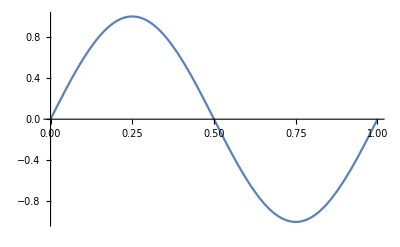
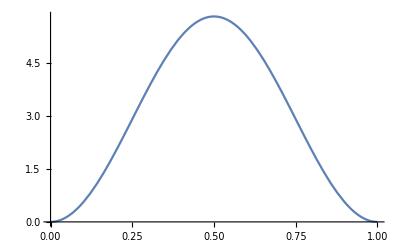

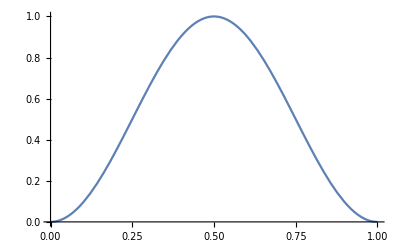
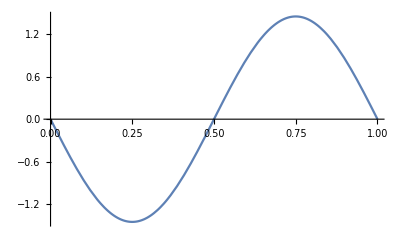

```mathematica
val={a0->2.5,τ->1,ζ->0.5,θ0->0,θ1->0,L->1,v0->0,v1->0,μ->1,n->1};
Simplify[eq1ϵ] (*check*)
Simplify[eq2ϵ] (*check*)

{Plot[θ1[z]//.val//.{A1->0,B1->1},{z,0,1}],Plot[v1[z]//.val//.{A1->0,B1->1},{z,0,1}]}
{Plot[θ1[z]//.val//.{A1->1,B1->0},{z,0,1}],Plot[v1[z]//.val//.{A1->1,B1->0},{z,0,1}]}
```

### b) Linearization around trivial solution (T_a= -1/2ρ μ ζ Ψ)

#### Solution of the linear problem

```mathematica
ClearAll["Global`*"]

sosϵ = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]->  ϵ v1''[z]};

eq1=4 (-1+a0^3)(-2 (1+a0^3) ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]])vx''[z]//.sosϵ;

eq2=(-1+a0^3) μ τ(1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z]+2 a0^2 k θ''[z]//.sosϵ;


eq1ϵ = Normal[Series[eq1,{ϵ,0,1}]]
eq2ϵ= Normal[Series[eq2,{ϵ,0,1}]]

sol = DSolve[{eq1ϵ==0,eq2ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
```

ϵ (-8 (-1+a0^3) (1+a0^3) ζ θ1'[z]+8 τ v1''[z])

ϵ (2 (-1+a0^3) μ τ v1'[z]+2 a0^2 k θ1''[z])

{{v1[z]→((a0^2 k C[4])/τ-(a0^2 k C[4] Cos[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)])/τ+(a0 √k √μ C[2] Sin[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)])/(√(1+a0^3) √ζ))/((-1+a0^3) μ),θ1[z]→(-√(1+a0^3) √μ τ C[2]+√(1+a0^3) √μ τ C[2] Cos[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)]+(a0+a0^4) √k √ζ C[4] Sin[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)])/((-1+a0^3) (1+a0^3)^(3/2) ζ √μ)}}

```mathematica
v[z_]:=1/((-1+a0^3) μ)((a0^2 k C[4])/τ(1- Cos[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)])+(a0 √k √μ C[2])/(√(1+a0^3) √ζ)Sin[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)]);
θ[z_]:=(√(1+a0^3) √μ τ C[2](Cos[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)]-1)+(a0+a0^4) √k √ζ C[4] Sin[((-1+a0^3) √(1+a0^3) z √ζ √μ)/(a0 √k)])/((-1+a0^3) (1+a0^3)^(3/2) ζ √μ);
```

```mathematica
(*Satisfy the other border conditions*)
FullSimplify[v[L]]
FullSimplify[θ[L]]
A={{a0^2 k/τ (1- Cos[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)])/((-1+a0^3) μ),(a0 √k √μ Sin[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)])/(√(1+a0^3) √ζ)}/((-1+a0^3) μ),{(a0+a0^4) √k √ζ Sin[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)]/((-1+a0^3) (1+a0^3)^(3/2) ζ √μ),√(1+a0^3) √μ τ ( Cos[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)]-1)/((-1+a0^3) (1+a0^3)^(3/2) ζ √μ)}};
FullSimplify[Det[A]]
```

(-(a0^2 k C[4] (-1+Cos[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)]))/τ+(a0 √k √μ C[2] Sin[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)])/(√(1+a0^3) √ζ))/((-1+a0^3) μ)

(√(1+a0^3) √μ τ C[2] (-1+Cos[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)])+(a0+a0^4) √k √ζ C[4] Sin[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)])/((-1+a0^3) (1+a0^3)^(3/2) ζ √μ)

(a0^2 k (-4 Sin[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(2 a0 √k)]^4-(-1+a0^3) μ Sin[((-1+a0^3) √(1+a0^3) L √ζ √μ)/(a0 √k)]^2))/((-1+a0^3)^3 (1+a0^3) ζ μ^2)

```mathematica
ClearAll["Global`*"]

Solve[((a0^3-1) √(1+a0^3)√ζ √μ)/(a0 √k)L==2n π,k]//FullSimplify 
sosϵ2 = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]-> ϵ v1''[z],k->((-1+a0^3)^2 (1+a0^3) L^2 ζ μ)/(4 a0^2 n^2 π^2)};
eq1=4 (-1+a0^3) (-2 (1+a0^3) ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]]) vx''[z];
eq2=(-1+a0^3) μ τ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z]+2 a0^2 k θ''[z];

eq1ϵ = Normal[Series[eq1//.sosϵ2,{ϵ,0,1}]]
eq2ϵ= Normal[Series[eq2//.sosϵ2,{ϵ,0,1}]]

DSolve[{eq1ϵ==0,eq2ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{k→((-1+a0^3)^2 (1+a0^3) L^2 ζ μ)/(4 a0^2 n^2 π^2)}}

ϵ (-8 (-1+a0^3) (1+a0^3) ζ θ1'[z]+8 τ v1''[z])

ϵ (2 (-1+a0^3) μ τ v1'[z]+((-1+a0^3)^2 (1+a0^3) L^2 ζ μ θ1''[z])/(2 n^2 π^2))

{{v1[z]→(L Sin[(n π z)/L] (2 n π τ C[2] Cos[(n π z)/L]+(-1+a0^6) L ζ C[4] Sin[(n π z)/L]))/(2 n^2 π^2 τ),θ1[z]→(2 τ C[2] Sin[(n π z)/L]^2)/(ζ-a0^6 ζ)+(L C[4] Sin[(2 n π z)/L])/(2 n π)}}

#### Solutions and plot (Numeric values for plotting, critical case n=1)

```mathematica
A1=(2 τ C[2])/(ζ(1-a0^6));B1=(L C[4])/(2 n π);A2=((-1+a0^6) L^2 ζ C[4])/(2 n^2 π^2 τ);B2=(L   C[2])/(2 n π);
FullSimplify[B2/A1]
FullSimplify[A2/B1]


Clear[A1,B1,A2,B2]
θ1[z_]= A1 Sin[(n π z)/L]^2+ B1 Sin[(2 n π z)/L];
v1[z_]= A2 Sin[(n π z)/L]^2+B2 Sin[(2n  π z)/L]/.{B2->  (L  ζ(1-a0^6))/(4 n π τ)A1,A2-> ((-1+a0^6)  ζ L)/(n π τ)  B1};
FullSimplify[v1[z]]
```

-((-1+a0^6) L ζ)/(4 n π τ)

((-1+a0^6) L ζ)/(n π τ)

((-1+a0^6) L ζ (4 B1 Sin[(n π z)/L]^2-A1 Sin[(2 n π z)/L]))/(4 n π τ)

0

0

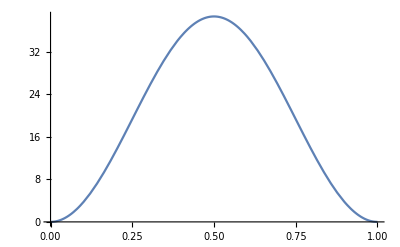
{-Graphics-,-Graphics-}

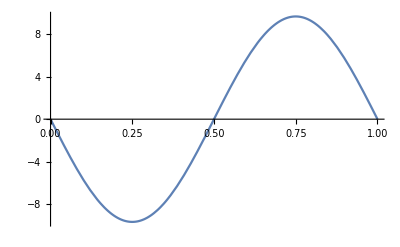
{-Graphics-,-Graphics-}

```mathematica
val={a0->2.5,τ->1,ζ->0.5,θ0->0,θ1->0,L->1,v0->0,v1->0,μ->1,n->1};
Simplify[eq1ϵ] (*check*)
Simplify[eq2ϵ] (*check*)
{Plot[θ1[z]//.val//.{A1->0,B1->1},{z,0,1}],Plot[v1[z]//.val//.{A1->0,B1->1},{z,0,1}]}
{Plot[θ1[z]//.val//.{A1->1,B1->0},{z,0,1}],Plot[v1[z]//.val//.{A1->1,B1->0},{z,0,1}]}
```

### c) Linearization around trivial solution (New boundary conditions)

#### Solution of the linear problem

```mathematica
ClearAll["Global`*"]
v[z_]:=1/((-1+a0^3) μ τ)(-a0^2 k Subscript[c, 1] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+1/(√ζ)√a0 √k √μ τ C[2] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)]);
θ[z_]:=1/(a0 (-1+a0^3) ζ)(τ Subscript[c, 2] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+1/(√μ)a0^(3/2) √k √ζ C[4] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)]);
```

```mathematica
Solve[(μ ρ τ *dv1L)/a0^2==0,dv1L]
```

{{dv1L→0}}

```mathematica
(*Satisfy the other border conditions*)
 v'[L](* Put to zero*)
θ[L] (* Put to zero*)
A={{  Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)], (a0^(3/2) √k √ζ)/(√μ τ) Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)]},{τ/(a0 (-1+a0^3) ζ)(-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]),(a0^(1/2) √k √ζ Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/((-1+a0^3) ζ √μ)}};

FullSimplify[Det[A]]
```

((-1+a0^3) μ τ C[2] Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]+a0^(3/2) (-1+a0^3) √k √ζ √μ Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)] c_1)/((-1+a0^3) μ τ)

((a0^(3/2) √k √ζ C[4] Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/(√μ)+τ (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]) c_2)/(a0 (-1+a0^3) ζ)

(√a0 √k Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/((-1+a0^3) √ζ √μ)

```mathematica
ClearAll["Global`*"]
Solve[((a0^3-1) L √ζ √μ)/(√a0 √k)==n π,k]//FullSimplify; (*Use the result inside the list of replacement*)
sosϵ2 = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]-> ϵ v1''[z],k->((-1+a0^3)^2 L^2 ζ μ)/(a0 n^2 π^2)};
"Check"
eq1=4 (-1+a0^3) (-2 a0 ζ Cos[2 θ[z]]+2 τ (1+a0^3+(-1+a0^3) Cos[2 θ[z]]) Sin[2 θ[z]] vx'[z]) θ'[z]-τ (-5+2 a0^3-5 a0^6+4 (-1+a0^6) Cos[2 θ[z]]+(-1+a0^3)^2 Cos[4 θ[z]]) vx''[z];
eq2=(-1+a0^3) μ τ (1-a0^3+(1+a0^3) Cos[2 θ[z]]) vx'[z]+2 a0^2 k θ''[z];
eq1ϵ = Normal[Series[eq1//.sosϵ2,{ϵ,0,1}]]
eq2ϵ= Normal[Series[eq2//.sosϵ2,{ϵ,0,1}]]

sol = DSolve[{eq1ϵ==0,eq2ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
Refine[FullSimplify[D[v1[z]/.sol[[1]],z]/.{z->L}],Element[n,Integers]]
Refine[FullSimplify[θ1[z]/.sol[[1]]/.{z->L}],Element[n,Integers]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Check

ϵ (-8 a0 (-1+a0^3) ζ θ1'[z]+8 τ v1''[z])

ϵ (2 (-1+a0^3) μ τ v1'[z]+(2 a0 (-1+a0^3)^2 L^2 ζ μ θ1''[z])/(n^2 π^2))

{{v1[z]→(L (-a0 (-1+a0^3) L ζ C[4] (-1+Cos[(n π z)/L])+n π τ C[2] Sin[(n π z)/L]))/(n^2 π^2 τ),θ1[z]→(τ C[2] (-1+Cos[(n π z)/L]))/(a0 (-1+a0^3) ζ)+(L C[4] Sin[(n π z)/L])/(n π)}}

(-1)^n C[2]

((-1+(-1)^n) τ C[2])/(a0 (-1+a0^3) ζ)

#### Solutions and plot (Numeric values for plotting, critical case n=1)

```mathematica
A1=(L C[4])/(n π);A2=(2L a0 (-1+a0^3) L ζ C[4])/(n^2 π^2 τ);
FullSimplify[A2/A1]

Clear[A1,B1,A2,B2]
θ1[z_]= A1 Sin[(n π z)/L];
v1[z_]= A2 Sin[(n π z)/(2L)]^2/.{A2->  (2 a0 (-1+a0^3) L ζ)/(n π τ)A1};
FullSimplify[v1[z]]
```

(2 a0 (-1+a0^3) L ζ)/(n π τ)

-(a0 (-1+a0^3) A1 L ζ (-1+Cos[(n π z)/L]))/(n π τ)

0

0

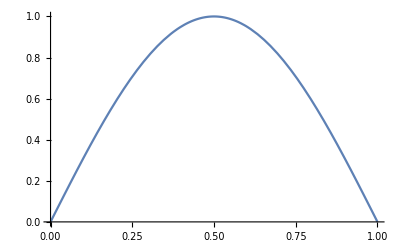
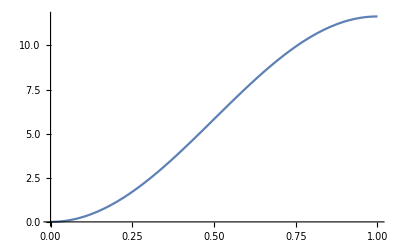
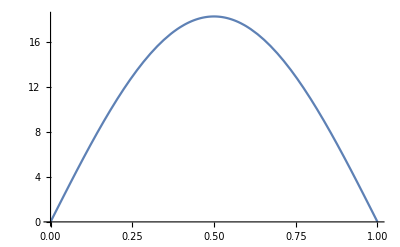

```mathematica
val={a0->2.5,τ->1,ζ->0.5,θ0->0,θ1->0,L->1,v0->0,v1->0,μ->1,n->1};
Simplify[eq1ϵ] (*check*)
Simplify[eq2ϵ] (*check*)

{Plot[θ1[z]//.val//.{A1->1},{z,0,1}],Plot[v1[z]//.val//.{A1->1},{z,0,1}],Plot[v1'[z]//.val//.{A1->1},{z,0,1}]}
```

### d) Linearization around trivial solution (Second relaxation time)

#### Solution of the linear problem

```mathematica
ClearAll["Global`*"]

(*Perturbtion around the null-solution*)
sosϵ1 = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]->  ϵ v1''[z]};

eq11=-4 (-2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+((2 (-1+a0^6) Sin[2 θ[z]]-(1+a0^3)^2 Sin[4 θ[z]]) Subscript[τ, 1]+a0^3 Sin[4 θ[z]] (Subscript[τ, 2]+3 Cos[2 w] Subscript[τ, d]+3 Subscript[τ, s])) vx'[z]) θ'[z]-2 ((1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 Subscript[τ, 1]+a0^3 Sin[2 θ[z]]^2 (Subscript[τ, 2]+3 Cos[2 w] Subscript[τ, d]+3 Subscript[τ, s])) vx''[z]//.sosϵ1;
eq12=(-1+a0^3) μ  (1-a0^3+(1+a0^3) Cos[2 θ[z]]) Subscript[τ, 1] vx'[z]+2 a0^3 k  θ''[z]//.sosϵ1;


eq21=4 (2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+(-2 (-1+a0^6) Sin[2 θ[z]] Subscript[τ, 1]+Sin[4 θ[z]] ((1+a0^3)^2 Subscript[τ, 1]-a0^3 Subscript[τ, 2])) vx'[z]) θ'[z]+(-2 (1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 Subscript[τ, 1]+a0^3 (-1+Cos[4 θ[z]]) Subscript[τ, 2]) vx''[z]//.sosϵ1;
eq22=(-1+a0^3) μ  (1-a0^3+(1+a0^3) Cos[2 θ[z]]) Subscript[τ, 1] vx'[z]+2 a0^3 k  θ''[z]//.sosϵ1;

eq11ϵ = Normal[Series[eq11,{ϵ,0,1}]]
eq12ϵ= Normal[Series[eq12,{ϵ,0,1}]]
eq21ϵ = Normal[Series[eq21,{ϵ,0,1}]]
eq22ϵ= Normal[Series[eq22,{ϵ,0,1}]]

sol1=DSolve[{eq11ϵ==0,eq12ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
sol2=DSolve[{eq21ϵ==0,eq22ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify

Clear[coefv,coeft]
coefv=CoefficientList[v1[z]//.sol1//.{z->L},{C[2],C[4]}];
coeft=CoefficientList[θ1[z]//.sol1//.{z->L},{C[2],C[4]}];
A1={{coefv[[1]][[1]][[2]],coefv[[1]][[2]][[1]]},{coeft[[1]][[1]][[2]],coeft[[1]][[2]][[1]]}}
FullSimplify[Det[A1]]

Clear[coefv,coeft]
coefv=CoefficientList[v1[z]//.sol2//.{z->L},{C[2],C[4]}];
coeft=CoefficientList[θ1[z]//.sol2//.{z->L},{C[2],C[4]}];
A2={{coefv[[1]][[1]][[2]],coefv[[1]][[2]][[1]]},{coeft[[1]][[1]][[2]],coeft[[1]][[2]][[1]]}}
FullSimplify[Det[A2]]
```

ϵ (8 a0^2 (-1+a0^3) ζ θ1'[z]-8 τ_1 v1''[z])

ϵ (2 (-1+a0^3) μ τ_1 v1'[z]+2 a0^3 k θ1''[z])

ϵ (8 a0^2 (-1+a0^3) ζ θ1'[z]-8 τ_1 v1''[z])

ϵ (2 (-1+a0^3) μ τ_1 v1'[z]+2 a0^3 k θ1''[z])

{{v1[z]→(-a0^3 k C[4] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+(√a0 √k √μ C[2] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)] τ_1)/(√ζ))/((-1+a0^3) μ τ_1),θ1[z]→((a0^(5/2) √k √ζ C[4] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)])/(√μ)+C[2] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)]) τ_1)/(a0^2 (-1+a0^3) ζ)}}

{{v1[z]→(-a0^3 k C[4] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)])+(√a0 √k √μ C[2] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)] τ_1)/(√ζ))/((-1+a0^3) μ τ_1),θ1[z]→((a0^(5/2) √k √ζ C[4] Sin[((-1+a0^3) z √ζ √μ)/(√a0 √k)])/(√μ)+C[2] (-1+Cos[((-1+a0^3) z √ζ √μ)/(√a0 √k)]) τ_1)/(a0^2 (-1+a0^3) ζ)}}

{{-(a0^3 k (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]))/((-1+a0^3) μ τ_1),(√a0 √k Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/((-1+a0^3) √ζ √μ)},{(√a0 √k Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/((-1+a0^3) √ζ √μ),((-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]) τ_1)/(a0^2 (-1+a0^3) ζ)}}

(2 a0 k (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]))/((-1+a0^3)^2 ζ μ)

{{-(a0^3 k (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]))/((-1+a0^3) μ τ_1),(√a0 √k Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/((-1+a0^3) √ζ √μ)},{(√a0 √k Sin[((-1+a0^3) L √ζ √μ)/(√a0 √k)])/((-1+a0^3) √ζ √μ),((-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]) τ_1)/(a0^2 (-1+a0^3) ζ)}}

(2 a0 k (-1+Cos[((-1+a0^3) L √ζ √μ)/(√a0 √k)]))/((-1+a0^3)^2 ζ μ)

```mathematica
ClearAll["Global`*"]

Solve[((a0^3-1) L √ζ √μ)/(√a0 √k)==2n π,k]//FullSimplify (*Use the result inside the list of replacement*)

(*Perturbtion around the null-solution*)
sosϵ1 = {θ[z]-> ϵ θ1[z],θ'[z]-> ϵ θ1'[z], θ''[z]-> ϵ θ1''[z],vx[z]-> ϵ v1[z], vx'[z]-> ϵ v1'[z], vx''[z]->  ϵ v1''[z],k->((-1+a0^3)^2 L^2 ζ μ)/(4 a0 n^2 π^2)};

eq11=-4 (-2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+((2 (-1+a0^6) Sin[2 θ[z]]-(1+a0^3)^2 Sin[4 θ[z]]) Subscript[τ, 1]+a0^3 Sin[4 θ[z]] (Subscript[τ, 2]+3 Cos[2 w] Subscript[τ, d]+3 Subscript[τ, s])) vx'[z]) θ'[z]-2 ((1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 Subscript[τ, 1]+a0^3 Sin[2 θ[z]]^2 (Subscript[τ, 2]+3 Cos[2 w] Subscript[τ, d]+3 Subscript[τ, s])) vx''[z]//.sosϵ1;
eq12=(-1+a0^3) μ  (1-a0^3+(1+a0^3) Cos[2 θ[z]]) Subscript[τ, 1] vx'[z]+2 a0^3 k  θ''[z]//.sosϵ1;

eq21=4 (2 a0^2 (-1+a0^3) ζ Cos[2 θ[z]]+(-2 (-1+a0^6) Sin[2 θ[z]] Subscript[τ, 1]+Sin[4 θ[z]] ((1+a0^3)^2 Subscript[τ, 1]-a0^3 Subscript[τ, 2])) vx'[z]) θ'[z]+(-2 (1-a0^3+(1+a0^3) Cos[2 θ[z]])^2 Subscript[τ, 1]+a0^3 (-1+Cos[4 θ[z]]) Subscript[τ, 2]) vx''[z]//.sosϵ1;
eq22=(-1+a0^3) μ  (1-a0^3+(1+a0^3) Cos[2 θ[z]]) Subscript[τ, 1] vx'[z]+2 a0^3 k  θ''[z]//.sosϵ1;


eq11ϵ = Normal[Series[eq11,{ϵ,0,1}]];
eq12ϵ= Normal[Series[eq12,{ϵ,0,1}]];
eq21ϵ = Normal[Series[eq21,{ϵ,0,1}]];
eq22ϵ= Normal[Series[eq22,{ϵ,0,1}]]; 

sol1=DSolve[{eq11ϵ==0,eq12ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
sol2=DSolve[{eq21ϵ==0,eq22ϵ==0,v1[0]==0,θ1[0]==0},{v1[z],θ1[z]},z]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{k→((-1+a0^3)^2 L^2 ζ μ)/(4 a0 n^2 π^2)}}

{{v1[z]→(L Sin[(n π z)/L] (a0^2 (-1+a0^3) L ζ C[4] Sin[(n π z)/L]+2 n π C[2] Cos[(n π z)/L] τ_1))/(2 n^2 π^2 τ_1),θ1[z]→Sin[(n π z)/L] ((L C[4] Cos[(n π z)/L])/(n π)+(2 C[2] Sin[(n π z)/L] τ_1)/(a0^2 ζ-a0^5 ζ))}}

{{v1[z]→(L Sin[(n π z)/L] (a0^2 (-1+a0^3) L ζ C[4] Sin[(n π z)/L]+2 n π C[2] Cos[(n π z)/L] τ_1))/(2 n^2 π^2 τ_1),θ1[z]→Sin[(n π z)/L] ((L C[4] Cos[(n π z)/L])/(n π)+(2 C[2] Sin[(n π z)/L] τ_1)/(a0^2 ζ-a0^5 ζ))}}

#### Solutions and plot (Numeric values for plotting, critical case n=1)

```mathematica
(*i*)
A1=(2 C[2] Subscript[τ, 1])/(a0^2 ζ-a0^5 ζ) ;B1=(L C[4])/(2n π);A2=(a0^2 (-1+a0^3) L^2 ζ C[4])/(2 n^2 π^2 Subscript[τ, 1]);B2=(L  C[2])/(2 n π);
B2/A1
A2/B1

Clear[A1,B1,A2,B2]
θ1[z_]= A1 Sin[(n π z)/L]^2+ B1 Sin[(2 n π z)/L];
v1[z_]= A2 Sin[(n π z)/L]^2+B2 Sin[(2n  π z)/L]/.{B2->  (L (a0^2 ζ-a0^5 ζ))/(4 n π Subscript[τ, 1])A1,A2-> (a0^2 (-1+a0^3) L ζ)/(n π Subscript[τ, 1])B1};
FullSimplify[v11[z]]
```

(L (a0^2 ζ-a0^5 ζ))/(4 n π τ_1)

(a0^2 (-1+a0^3) L ζ)/(n π τ_1)

v11[z]

0

0

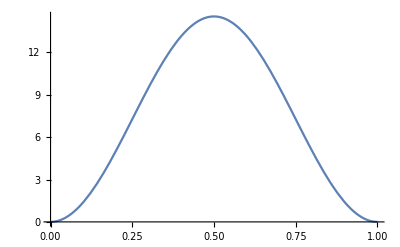
{-Graphics-,-Graphics-}

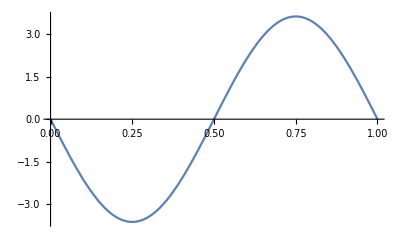
{-Graphics-,-Graphics-}

```mathematica
val={a0->2.5,Subscript[τ, 1]->1,ζ->0.5,θ0->0,θ1->0,L->1,v0->0,v1->0,μ->1,n->1};
Simplify[eq11ϵ] (*check*)
Simplify[eq12ϵ] (*check*)

{Plot[θ1[z]//.val//.{A1->0,B1->1},{z,0,1}],Plot[v1[z]//.val//.{A1->0,B1->1},{z,0,1}]}
{Plot[θ1[z]//.val//.{A1->1,B1->0},{z,0,1}],Plot[v1[z]//.val//.{A1->1,B1->0},{z,0,1}]}
```